```mathematica
(*Preliminary Global Definitions*)
Assign[vars_,vals_]:=Table[vars[[i]]-> vals[[i]],{i,Length[vars]}];
Phi[σ_,x_,p_]:=If[x===1,(x+1)^p,(x+1)^p+σ(x-1)^p];
G[x_,p_]:=2^p/Phi[-1,x,p];
Λ[x_,p_]:=If[x===1,1,Phi[1,x,p]/Phi[-1,x,p]];
```

```mathematica
evaluateQs[vecsA_,valsA_,vecsB_,valsB_,meanA_,meanB_,OptionsPattern[{Assmps-> {},VBExpansion-> False(*,finalassmps-> {}*)}]]:=With[{n=Length[meanA]/2,dvec=meanB-meanA},
Clear[qs];
Print["Lambda of alphas: ",Λ[#,s]&/@valsA//MatrixForm];
With[{VAs=vecsA.DiagonalMatrix[Join[#,#]&@(Λ[#,s]&/@valsA)].vecsAᵀ,
VB1ms=vecsB.DiagonalMatrix[Join[#,#]&@(Λ[#,1-s]&/@valsB)].vecsBᵀ//If[OptionValue[VBExpansion],Series[#,{d,0,2}]&,Identity],assumptions={0<s<1}~Join~OptionValue[Assmps]},
Print["Assumptions: ",assumptions];
With[{qbars=2^n Simplify[Product[G[valsA[[k]],s]  G[valsB[[k]],1-s],{k,1,n}],Assumptions->assumptions]/Simplify[√Det[VAs+VB1ms],Assumptions->assumptions],
wigners=Exp[-1/2{dvec}.Inverse[VAs+VB1ms].{dvec}ᵀ]//Last//Last//Simplify[#,Assumptions->assumptions]&},
qs=qbars*wigners//FullSimplify[#,Assumptions->(*OptionValue[finalassmps]~Join~*)assumptions]&]]];
```

Use Qsijcomp (with vecsi and vecsj equal to the symplectic eigenvectors of the undisplaced and displaced covariance matrix respectively) in chernoff-exponent to get the Chernoff bound in the non-perturbative regime of displacement.

Beam Displacement Problem Setup

-Graphics-

```mathematica
(*Subscript[ϵ, 0], Subscript[ϵ, 1], and η are functions of the probe spatial mode, which is parameterized by HG-basis expansion coefficients. The expressions are given in the function Compilefunctions below*)
(* θ can be set to zero, since it does not affect the separability of the final state under the two hypotheses δ=0 and δ=d*)
(*To resolve negative chernoff expression try evaluating Qs numerically for small d (s=1/2) without any expansions using the parameters that give negative with current functions*)
```

```mathematica
covTrace[#.IdentityMatrix[4].#†,{2}]&@qqpptoqpqp@(atoq[2].BSgen[2,1,2,κ].SMSgen2[2,{s,0},0])//FullSimplify[#,Assumptions->( 1>#>0&/@{κ,s})]&//MatrixForm
```

(1+(-1+ⅇ^(-4 s)) κ | 0
0 | 1+(-1+ⅇ^(4 s)) κ)

```mathematica
initV=({{η E^(-2r)+1-η, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, η E^(2r)+1-η, 0}, {0, 0, 0, 1}});
initmean=√η{q1,0,p1,0};
(*Subscript[ϵ, 1]=√(ϵ^2-Subscript[ϵ, 0]^2);*)
(*Mean photon number constraint: Sinh[r]^2+q1^2+q2^2 = hbar N where hbar is 2*)
bog= ({{1-I ϵ0 d, d ϵ1}, {-d ϵ1, 1}})-IdentityMatrix[2]//MatrixExp;
transaa1=SparseArray[{Band[{1,1},{2,2}]-> bog,Band[{3,3},{4,4}]-> bog*}]//Normal//FullSimplify[#,Assumptions-> {d∈Reals,ϵ0∈Reals,ϵ1∈Reals}]&;
transaa2=BSgen2[2,1,2,d ϵ1,π].Phasegen[{ϵ0 d,0}]//FullSimplify[#,Assumptions-> {d∈Reals,ϵ0∈Reals,ϵ1∈Reals}]&;
Series[transaa1,{d,0,2}]//FullSimplify[#,Assumptions-> {d∈Reals,ϵ0∈Reals,ϵ1∈Reals}]&//TraditionalForm//MatrixForm//Print["Unitary generated by infinitesimal\n Bogoliubov transformation: ",#]&;
Series[transaa2,{d,0,2}]//MatrixForm//Print["Valid approximation of unitary generated by infinitesimal\n Bogoliubov transforamtion in small d limit: ",#]&;
trans=atoq[2].transaa2.ConjugateTranspose[atoq[2]]//FullSimplify[#,Assumptions-> {d∈Reals,ϵ0∈Reals,ϵ1∈Reals}]&;
Print["qqpp form of final transformation: ",trans//MatrixForm];
```

Unitary generated by infinitesimal
 Bogoliubov transformation: (1-ⅈ d ϵ0+1/2 d^2 (-ϵ0^2-ϵ1^2)+O(d^3) | d ϵ1-1/2 ⅈ d^2 ϵ0 ϵ1+O(d^3) | 0 | 0
-d ϵ1+1/2 ⅈ d^2 ϵ0 ϵ1+O(d^3) | 1-(d^2 ϵ1^2)/2+O(d^3) | 0 | 0
0 | 0 | 1+1/2 ⅈ d (ϵ0 Conjugate[(1/(√(-ϵ0^2-4 ϵ1^2)))] Conjugate[√(-ϵ0^2-4 ϵ1^2)]+ϵ0)+1/8 d^2 (-2 ϵ0^2 Conjugate[(1/(√(-ϵ0^2-4 ϵ1^2)))] Conjugate[√(-ϵ0^2-4 ϵ1^2)]+(Conjugate[√(-ϵ0^2-4 ϵ1^2)])^2-ϵ0^2)+O(d^3) | d ϵ1 Conjugate[(1/(√(-ϵ0^2-4 ϵ1^2)))] Conjugate[√(-ϵ0^2-4 ϵ1^2)]+1/2 ⅈ d^2 ϵ0 ϵ1 Conjugate[(1/(√(-ϵ0^2-4 ϵ1^2)))] Conjugate[√(-ϵ0^2-4 ϵ1^2)]+O(d^3)
0 | 0 | -d ϵ1 Conjugate[(1/(√(-ϵ0^2-4 ϵ1^2)))] Conjugate[√(-ϵ0^2-4 ϵ1^2)]-1/2 ⅈ d^2 ϵ0 ϵ1 Conjugate[(1/(√(-ϵ0^2-4 ϵ1^2)))] Conjugate[√(-ϵ0^2-4 ϵ1^2)]+O(d^3) | 1-1/2 ⅈ d ϵ0 (Conjugate[(1/(√(-ϵ0^2-4 ϵ1^2)))] Conjugate[√(-ϵ0^2-4 ϵ1^2)]-1)+1/8 d^2 (2 ϵ0^2 Conjugate[(1/(√(-ϵ0^2-4 ϵ1^2)))] Conjugate[√(-ϵ0^2-4 ϵ1^2)]+(Conjugate[√(-ϵ0^2-4 ϵ1^2)])^2-ϵ0^2)+O(d^3))

Valid approximation of unitary generated by infinitesimal
 Bogoliubov transforamtion in small d limit: (1-ⅈ ϵ0 d+(-ϵ0^2/2-ϵ1^2/2) d^2+O[d]^3 | ϵ1 d+O[d]^3 | 0 | 0
-ϵ1 d+ⅈ ϵ0 ϵ1 d^2+O[d]^3 | 1-(ϵ1^2 d^2)/2+O[d]^3 | 0 | 0
0 | 0 | 1+ⅈ ϵ0 d+(-ϵ0^2/2-ϵ1^2/2) d^2+O[d]^3 | ϵ1 d+O[d]^3
0 | 0 | -ϵ1 d-ⅈ ϵ0 ϵ1 d^2+O[d]^3 | 1-(ϵ1^2 d^2)/2+O[d]^3)

qqpp form of final transformation: (Cos[d ϵ0] Cos[d ϵ1] | Sin[d ϵ1] | Cos[d ϵ1] Sin[d ϵ0] | 0
-Cos[d ϵ0] Sin[d ϵ1] | Cos[d ϵ1] | -Sin[d ϵ0] Sin[d ϵ1] | 0
-Cos[d ϵ1] Sin[d ϵ0] | 0 | Cos[d ϵ0] Cos[d ϵ1] | Sin[d ϵ1]
Sin[d ϵ0] Sin[d ϵ1] | 0 | -Cos[d ϵ0] Sin[d ϵ1] | Cos[d ϵ1])

```mathematica
finalV=trans.initV.transᵀ;
finalV//FullSimplify//MatrixForm
```

(Cos[d ϵ1]^2 (1-η+ⅇ^(-2 r) η Cos[d ϵ0]^2+ⅇ^(2 r) η Sin[d ϵ0]^2)+Sin[d ϵ1]^2 | 1/2 η Sin[2 d ϵ1] (-2 Sinh[r]^2+Cos[2 d ϵ0] Sinh[2 r]) | η Cos[d ϵ1]^2 Sin[2 d ϵ0] Sinh[2 r] | -1/2 η Sin[2 d ϵ0] Sin[2 d ϵ1] Sinh[2 r]
1/2 η Sin[2 d ϵ1] (-2 Sinh[r]^2+Cos[2 d ϵ0] Sinh[2 r]) | Cos[d ϵ1]^2+ⅇ^(-2 r) η Cos[d ϵ0]^2 Sin[d ϵ1]^2+(1-η+ⅇ^(2 r) η Sin[d ϵ0]^2) Sin[d ϵ1]^2 | -1/2 η Sin[2 d ϵ0] Sin[2 d ϵ1] Sinh[2 r] | η Sin[2 d ϵ0] Sin[d ϵ1]^2 Sinh[2 r]
η Cos[d ϵ1]^2 Sin[2 d ϵ0] Sinh[2 r] | -1/2 η Sin[2 d ϵ0] Sin[2 d ϵ1] Sinh[2 r] | Cos[d ϵ1]^2 (1-η+ⅇ^(2 r) η Cos[d ϵ0]^2+ⅇ^(-2 r) η Sin[d ϵ0]^2)+Sin[d ϵ1]^2 | -1/2 η Sin[2 d ϵ1] (2 Sinh[r]^2+Cos[2 d ϵ0] Sinh[2 r])
-1/2 η Sin[2 d ϵ0] Sin[2 d ϵ1] Sinh[2 r] | η Sin[2 d ϵ0] Sin[d ϵ1]^2 Sinh[2 r] | -1/2 η Sin[2 d ϵ1] (2 Sinh[r]^2+Cos[2 d ϵ0] Sinh[2 r]) | Cos[d ϵ1]^2+ⅇ^(-2 r) (-ⅇ^(2 r) (-1+η)+ⅇ^(4 r) η Cos[d ϵ0]^2+η Sin[d ϵ0]^2) Sin[d ϵ1]^2)

```mathematica
finalmean=trans.initmean//FullSimplify;
finalmean//TraditionalForm
```

{√η cos(d ϵ1) (p1 sin(d ϵ0)+q1 cos(d ϵ0)),-√η sin(d ϵ1) (p1 sin(d ϵ0)+q1 cos(d ϵ0)),√η cos(d ϵ1) (p1 cos(d ϵ0)-q1 sin(d ϵ0)),√η sin(d ϵ1) (q1 sin(d ϵ0)-p1 cos(d ϵ0))}

Symplectic Decomposition of initV

```mathematica
(1+(E^(-2r)-1)η)(1+(E^(2r)-1)η)-(Cosh[r]^2-(1-2η)^2 Sinh[r]^2)//Simplify
```

0

```mathematica
(*Note: A^4 B^4-1 = Cosh[r]^2+4η(1-η)Sinh[r]^2*)
```

```mathematica
initsympvals={(A B)^2,1};
(*A=(1+(E^(-2r)-1)η)^(1/4),B=(1+(E^(2r)-1)η)^(1/4)*)
S1=A/B;
initsympvecs=DiagonalMatrix[{S1,1,S1^-1,1}];
```

```mathematica
initsympvecs.DiagonalMatrix[Join[#,#]&@initsympvals].initsympvecsᵀ//MatrixForm
```

(A^4 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | B^4 | 0
0 | 0 | 0 | 1)

```mathematica
finalsympvecs=trans.initsympvecs//FullSimplify;
```

```mathematica
finalsympvecs//MatrixForm
```

((A Cos[d ϵ0] Cos[d ϵ1])/B | Sin[d ϵ1] | (B Cos[d ϵ1] Sin[d ϵ0])/A | 0
-(A Cos[d ϵ0] Sin[d ϵ1])/B | Cos[d ϵ1] | -(B Sin[d ϵ0] Sin[d ϵ1])/A | 0
-(A Cos[d ϵ1] Sin[d ϵ0])/B | 0 | (B Cos[d ϵ0] Cos[d ϵ1])/A | Sin[d ϵ1]
(A Sin[d ϵ0] Sin[d ϵ1])/B | 0 | -(B Cos[d ϵ0] Sin[d ϵ1])/A | Cos[d ϵ1])

```mathematica
(*Sanity check that final V can be obtained by transforming the symplectic eigenvectors (since transformation is unitary)*)
(finalsympvecs.DiagonalMatrix[Join[#,#]&@initsympvals].finalsympvecsᵀ/.{A->(1+(E^(-2r)-1)η)^(1/4),B-> (1+(E^(2r)-1)η)^(1/4) })-finalV//Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ClearParams[];
evaluateQs[finalsympvecs/.d-> 0,initsympvals/.d-> 0,finalsympvecs,initsympvals,initmean,finalmean,Assmps-> {(A^2 B^2-1)^s<(A^2 B^2+1)^s,A^2 B^2>1,A>0,B>0},VBExpansion-> True(*,finalassmps->{(A^2 B^2-1)^s<(A^2 B^2+1)^s}*) ];
```

Lambda of alphas: (((-1+A^2 B^2)^s+(1+A^2 B^2)^s)/(-(-1+A^2 B^2)^s+(1+A^2 B^2)^s)
1)

Assumptions: {0<s<1,(-1+A^2 B^2)^s<(1+A^2 B^2)^s,A^2 B^2>1,A>0,B>0}

```mathematica
qs
```

-1/Sign[(-1+A^2 B^2)^(2 s) (1+A^2 B^2)+(-1+A^2 B^2) (1+A^2 B^2)^(2 s)-2 A^2 B^2 (-1+A^4 B^4)^s]+((A^12 B^4 ϵ0^2+B^8 ϵ0^2+A^8 (4 B^4 ϵ1^2+ϵ0^2 (1-2 B^8+4 B^4 q1^2 η))+A^4 B^4 (ϵ0^2 (-2+B^8+4 B^4 p1^2 η)+4 ϵ1^2 (-2+B^4+(p1^2+q1^2) η))+ϵ0^2 (-4 A^4 B^4 (B^4 p1^2+A^4 q1^2) η Cosh[s Log[1-2/(1+A^2 B^2)]]-(A^4-B^4)^2 (1+A^4 B^4) Cosh[2 s Log[1-2/(1+A^2 B^2)]]+2 A^2 B^2 (-2 (B^4 p1^2+A^4 q1^2) η Sinh[s Log[1-2/(1+A^2 B^2)]]-(A^4-B^4)^2 Sinh[2 s Log[1-2/(1+A^2 B^2)]]))) d^2)/(16 A^4 B^4 Sign[(-1+A^2 B^2)^s-(1+A^2 B^2)^s] Sign[(-1+A^2 B^2)^s (1+A^2 B^2)+(1-A^2 B^2) (1+A^2 B^2)^s])+O[d]^3

```mathematica
qssimpcoeffd2=SeriesCoefficient[qs,2]//FullSimplify[#,Assumptions->{0<s<1,Sign[(-1+A^2 B^2)^s-(1+A^2 B^2)^s]==-1,Sign[(-1+A^2 B^2)^s (1+A^2 B^2)+(1-A^2 B^2) (1+A^2 B^2)^s]==1,A^2 B^2>1,A>0,B>0}]&
```

-1/(16 A^4 B^4)(A^12 B^4 ϵ0^2+B^8 ϵ0^2+A^8 (4 B^4 ϵ1^2+ϵ0^2 (1-2 B^8+4 B^4 q1^2 η))+A^4 B^4 (ϵ0^2 (-2+B^8+4 B^4 p1^2 η)+4 ϵ1^2 (-2+B^4+(p1^2+q1^2) η))+ϵ0^2 (-4 A^4 B^4 (B^4 p1^2+A^4 q1^2) η Cosh[s Log[1-2/(1+A^2 B^2)]]-(A^4-B^4)^2 (1+A^4 B^4) Cosh[2 s Log[1-2/(1+A^2 B^2)]]+2 A^2 B^2 (-2 (B^4 p1^2+A^4 q1^2) η Sinh[s Log[1-2/(1+A^2 B^2)]]-(A^4-B^4)^2 Sinh[2 s Log[1-2/(1+A^2 B^2)]])))

```mathematica
qssimp=1+qssimpcoeffd2 d^2//Collect[#,d]&;
qssimp//TraditionalForm
```

1-1/(16 A^4 B^4)d^2 (A^12 B^4 ϵ0^2+A^8 (4 B^4 ϵ1^2+ϵ0^2 (-2 B^8+4 B^4 η q1^2+1))+A^4 B^4 (4 ϵ1^2 (B^4+η (p1^2+q1^2)-2)+ϵ0^2 (B^8+4 B^4 η p1^2-2))+ϵ0^2 (2 A^2 B^2 ((A^4-B^4)^2 (-sinh(2 s log(1-2/(A^2 B^2+1))))-2 η (A^4 q1^2+B^4 p1^2) sinh(s log(1-2/(A^2 B^2+1))))-4 A^4 B^4 η (A^4 q1^2+B^4 p1^2) cosh(s log(1-2/(A^2 B^2+1)))-(A^4-B^4)^2 (A^4 B^4+1) cosh(2 s log(1-2/(A^2 B^2+1))))+B^8 ϵ0^2)

```mathematica
qssimpshalf=qssimp/.s-> 1/2//FullSimplify[#,Assumptions->{0<s<1,A^2 B^2>1,A>0,B>0}]&;
qssimpshalf//TraditionalForm
```

-(A^8 d^2 (ϵ0^2 (2 B^4 η q1^2+1)+2 B^4 ϵ1^2)+2 A^4 B^4 (d^2 (ϵ1^2 (B^4+η (p1^2+q1^2)-2)+ϵ0^2 (B^4 η p1^2-1))-4)-2 A^6 B^2 d^2 η q1^2 ϵ0^2 √(A^4 B^4-1)-2 A^2 B^6 d^2 η p1^2 ϵ0^2 √(A^4 B^4-1)+B^8 d^2 ϵ0^2)/(8 A^4 B^4)

```mathematica
qssimpcoeffd2/.s-> 1/2//Collect[#,{ϵ0,ϵ1}]&//List@@#&//FullSimplify[#,Assumptions->{A^2 B^2>1,A>0,B>0}]&(*//Plus@@#&*)
```

{-1/4 ϵ1^2 (-2+A^4+B^4+(p1^2+q1^2) η),-(ϵ0^2 ((A^4-B^4)^2-2 A^2 B^6 √(-1+A^4 B^4) p1^2 η-2 A^6 B^2 √(-1+A^4 B^4) q1^2 η+2 A^4 B^4 (B^4 p1^2+A^4 q1^2) η))/(8 A^4 B^4)}

```mathematica
qssimpcoeffd2shalf=qssimpcoeffd2/.s-> 1/2//Collect[#,{ϵ0,ϵ1}]&//List@@#&//FullSimplify[#,Assumptions->{0<s<1,A^2 B^2>1,A>0,B>0}]&//Sort(*sort list of terms by size of expression to standardize order across Mathematica versions*)//#[[1]]+(1/ϵ0^2#[[2]]//Collect[#,√(A^4 B^4-1)]&//List@@#&//FullSimplify[#,Assumptions->{A>0,B>0}]&//Plus@@#&//ϵ0^2 #&)&;
qssimpcoeffd2shalf//TraditionalForm (*If Qs≈1+αd^2, this expression is equal to α. The relationship to the QCE is Subscript[ξ, Q]=-ln(Subscript[Q, S])≈-αd^2*)
```

ϵ0^2 (1/8 (-2 η (A^4 q1^2+B^4 p1^2)-(A^8+B^8)/(A^4 B^4)+2)+(η √(A^4 B^4-1) (A^4 q1^2+B^4 p1^2))/(4 A^2 B^2))-1/4 ϵ1^2 (A^4+B^4+η (p1^2+q1^2)-2)

```mathematica
ClearParams[];
qssimpcoeffd2shalfROBUST=qssimpcoeffd2shalf/.(A^4 B^4-1)->Max[ 0.,A^4 B^4-1];
(*More robust version of the original variable to prevent numerical errors when compiled with real-typed arguments*)
qssimpcoeffd2shalfROBUST//TraditionalForm
```

ϵ0^2 ((η √(max(0.,A^4 B^4-1)) (A^4 q1^2+B^4 p1^2))/(4 A^2 B^2)+1/8 (-2 η (A^4 q1^2+B^4 p1^2)-(A^8+B^8)/(A^4 B^4)+2))-1/4 ϵ1^2 (A^4+B^4+η (p1^2+q1^2)-2)

```mathematica
highlevelfuncargs={r,q1,p1,η,ϵ0,ϵsq};
(*high-level gradient of α. Must be dotted by the matrix D[highlevelfuncargs,funcargsreduced]ᵀ to produce the gradient with respect to low-level arguments. Crucially: A and B depend on η.*)
highgradqssimpcoeffd2shalfROBUST=D[qssimpcoeffd2shalf/.{A-> (1+(E^(-2r)-1) η)^(1/4),B-> (1+(E^(2r)-1) η)^(1/4), ϵ1^2-> ϵsq-ϵ0^2},#]&/@highlevelfuncargs/.{ (1+(-1+ⅇ^(2 r)) η)-> A^4,(1+(-1+ⅇ^(-2 r)) η)-> B^4}(*//FullSimplify[#,Assumptions->{A>0,B>0,r>0,0<η<1}]&*)/.(A^4 B^4-1)->Max[1.*^-15 ,A^4 B^4-1]
```

{-1/4 (-ϵ0^2+ϵsq) (-2 ⅇ^(-2 r) η+2 ⅇ^(2 r) η)+ϵ0^2 (1/8 (-(2 (A^8+B^8) ⅇ^(-2 r) η)/(A^4 B^8)+(2 (A^8+B^8) ⅇ^(2 r) η)/(A^8 B^4)-(-4 B^4 ⅇ^(-2 r) η+4 A^4 ⅇ^(2 r) η)/(A^4 B^4)-2 η (2 ⅇ^(2 r) p1^2 η-2 ⅇ^(-2 r) q1^2 η))+((A^4 p1^2+B^4 q1^2) η (-2 A^4 ⅇ^(-2 r) η+2 B^4 ⅇ^(2 r) η))/(8 √(A^4) √(B^4) √Max[1.×10^-15,-1+A^4 B^4])+(ⅇ^(-2 r) (A^4 p1^2+B^4 q1^2) η^2 √Max[1.×10^-15,-1+A^4 B^4])/(4 √(A^4) (B^4)^(3/2))-(ⅇ^(2 r) (A^4 p1^2+B^4 q1^2) η^2 √Max[1.×10^-15,-1+A^4 B^4])/(4 (A^4)^(3/2) √(B^4))+(η (2 ⅇ^(2 r) p1^2 η-2 ⅇ^(-2 r) q1^2 η) √Max[1.×10^-15,-1+A^4 B^4])/(4 √(A^4) √(B^4))),-1/2 q1 (-ϵ0^2+ϵsq) η+ϵ0^2 (-1/2 B^4 q1 η+(√(B^4) q1 η √Max[1.×10^-15,-1+A^4 B^4])/(2 √(A^4))),-1/2 p1 (-ϵ0^2+ϵsq) η+ϵ0^2 (-1/2 A^4 p1 η+(√(A^4) p1 η √Max[1.×10^-15,-1+A^4 B^4])/(2 √(B^4))),-1/4 (-2+ⅇ^(-2 r)+ⅇ^(2 r)+p1^2+q1^2) (-ϵ0^2+ϵsq)+ϵ0^2 (1/8 (((A^8+B^8) (-1+ⅇ^(-2 r)))/(A^4 B^8)+((A^8+B^8) (-1+ⅇ^(2 r)))/(A^8 B^4)-(2 B^4 (-1+ⅇ^(-2 r))+2 A^4 (-1+ⅇ^(2 r)))/(A^4 B^4)-2 (A^4 p1^2+B^4 q1^2)-2 ((-1+ⅇ^(2 r)) p1^2+(-1+ⅇ^(-2 r)) q1^2) η)+((A^4 (-1+ⅇ^(-2 r))+B^4 (-1+ⅇ^(2 r))) (A^4 p1^2+B^4 q1^2) η)/(8 √(A^4) √(B^4) √Max[1.×10^-15,-1+A^4 B^4])+((A^4 p1^2+B^4 q1^2) √Max[1.×10^-15,-1+A^4 B^4])/(4 √(A^4) √(B^4))-((-1+ⅇ^(-2 r)) (A^4 p1^2+B^4 q1^2) η √Max[1.×10^-15,-1+A^4 B^4])/(8 √(A^4) (B^4)^(3/2))-((-1+ⅇ^(2 r)) (A^4 p1^2+B^4 q1^2) η √Max[1.×10^-15,-1+A^4 B^4])/(8 (A^4)^(3/2) √(B^4))+(((-1+ⅇ^(2 r)) p1^2+(-1+ⅇ^(-2 r)) q1^2) η √Max[1.×10^-15,-1+A^4 B^4])/(4 √(A^4) √(B^4))),1/2 ϵ0 ((-1+ⅇ^(-2 r)) η+(-1+ⅇ^(2 r)) η+(p1^2+q1^2) η)+2 ϵ0 (1/8 (2-(A^8+B^8)/(A^4 B^4)-2 (A^4 p1^2+B^4 q1^2) η)+((A^4 p1^2+B^4 q1^2) η √Max[1.×10^-15,-1+A^4 B^4])/(4 √(A^4) √(B^4))),1/4 (-((-1+ⅇ^(-2 r)) η)-(-1+ⅇ^(2 r)) η-(p1^2+q1^2) η)}

```mathematica
qssimpcoeffd2shalfrqp=qssimpcoeffd2shalf/.{A-> (1+(E^(-2r)-1) η)^(1/4),B-> (1+(E^(2r)-1) η)^(1/4)}//Simplify[#,Assumptions->(Join[{0<η<1},#>0&/@{r,p1^2,q1^2,ϵ0^2,ϵ1^2}])]&;
qssimpcoeffd2shalfrqp//TraditionalForm(*FullSimplify does not halt*)
```

1/8 (ϵ0^2 (2 η ⅇ^(-3 r) (ⅇ^(2 r)-1) √(-((η-1) η)/((η (ⅇ^(-2 r)-1)+1) (η (ⅇ^(2 r)-1)+1))) (-(η-1) ⅇ^(2 r) (p1^2+q1^2)+η p1^2 ⅇ^(4 r)+η q1^2)-2 η (p1^2 (η (ⅇ^(2 r)-1)+1)+q1^2 (η (ⅇ^(-2 r)-1)+1))-(η (ⅇ^(-2 r)-1)+1)/(η (ⅇ^(2 r)-1)+1)-(η (ⅇ^(2 r)-1)+1)/(η (ⅇ^(-2 r)-1)+1)+2)-2 η ⅇ^(-2 r) ϵ1^2 (ⅇ^(2 r) (p1^2+q1^2-2)+ⅇ^(4 r)+1))

```mathematica
(*No squeezing case depends linearly on the total mean photon number*)
qssimpcoeffd2shalfrqp/.{r->0,η-> 1}//Simplify
```

-1/4 (p1^2+q1^2) (ϵ0^2+ϵ1^2)

```mathematica
qssimpcoeffd2shalfrqp/.{q1-> 0,p1-> 0,η-> 1}//Simplify
(*need this to be negative for all r*)
```

-1/8 ⅇ^(-4 r) (-1+ⅇ^(2 r))^2 ((1+ⅇ^(2 r))^2 ϵ0^2+2 ⅇ^(2 r) ϵ1^2)

```mathematica
(*↑Asymptotically approximated by e^(4r)ϵ0^2+2 e^(2r)ϵ1^2*)
```

```mathematica
(*Showing that α scales like the mean photon number squared ((Sinh[r]^2)^2≈E^(4r)) in the pure squeezing, lossless case*)
Limit[(qssimpcoeffd2shalfrqp/.{q1-> 0,p1-> 0,η-> 1})/E^(4 r)//Simplify[#,Assumptions->r>0]&,r-> Infinity,Assumptions->{ϵ0^2>0,ϵ1^2>0}]
```

-ϵ0^2/8

```mathematica
(*Note that ϵ0^2 vanishes if the excited probe mode is orthogonal to its own derivative w.r.t. d(equivalent to the mode having a definite parity—even or odd—for displacement(d)-parameterized unitary mode transformations). This is why adding squeezing to the optimal classical solution (which happens to be a symmetric spatial mode) does not change the Chernoff exponent. In contrast, re-allocation of squeezing into displacement for the optimal spatial mode with sqeezing allowed will have an effect on the QCE*)
```

```mathematica
qssimpcoeffd2shalfrqp/.{q1-> 0,p1-> 0}//FullSimplify//TraditionalForm//Print;
(*↓Coefficient of ϵ0^2 in purely squeezed α*)
SeriesCoefficient[qssimpcoeffd2shalfrqp/.{q1->0,p1-> 0},{ϵ0,0,2}]//FullSimplify[#,Assumptions->(Join[{0<η<1},#>0&/@{r,ϵ0^2,ϵ1^2}])]&
```

1/8 η ⅇ^(-2 r) ((η (ⅇ^(4 r)-1)^2 ϵ0^2)/(((η-1) ⅇ^(2 r)-η) (η (ⅇ^(2 r)-1)+1))-2 (ⅇ^(2 r)-1)^2 ϵ1^2)

-(η^2 Sinh[2 r]^2)/(2 Cosh[r]^2-2 (1-2 η)^2 Sinh[r]^2)

```mathematica
Cosh[2r]//TrigExpand
```

Cosh[r]^2+Sinh[r]^2

```mathematica
Sinh[2 r]//TrigExpand
```

2 Cosh[r] Sinh[r]

```mathematica
(*how do the ratios of(η^2 Sinh[2 r]^2)/(2 Cosh[r]^2-2 (1-2 η)^2 Sinh[r]^2) to the total photon # Subscript[N, tot]=Sinh[r]^2 and Subscript[N, tot]^2 scale like in Subscript[N, tot]?*)
Limit[2 η^2 Coth[r]^2#/(Cosh[r]^2-(1-2 η)^2 Sinh[r]^2)(*/.η-> 1*),r-> ∞]&/@{Sinh[r]^2,1}//TableForm[{#}]&
```

η/(2-2 η) | 0

```mathematica
(*Note that the denominator 2-2η vanishes for the ratio w.r.t. Subscript[N, tot] if η=1. Setting η=1 before taking the limit results in a finite nonzero constant, showing that the lossless case scales like Subscript[N, tot]^2. In other words, even a small amount of loss destroys the N^2 scaling.*)
```

```mathematica
initsympvals
```

{A^2 B^2,1}

```mathematica
initmean
```

{q1 √η,0,p1 √η,0}

```mathematica
initsympvecs
```

{{A/B,0,0,0},{0,1,0,0},{0,0,B/A,0},{0,0,0,1}}

```mathematica
(*Same sign error made in evaluation of A and B below*)
```

```mathematica
{ϵ0coeffs,ϵcoeffs}=SeriesCoefficient[qssimpcoeffd2/.ϵ1^2-> (ϵ^2-ϵ0^2),{#,0,2}]&/@{ϵ0,ϵ};
{ϵ0coeffshalf,ϵcoeffshalf}=FullSimplify[#/.s-> 1/2,Assumptions->{0<s<1,A^2 B^2>1,A>0,B>0}]&/@{ϵ0coeffs,ϵcoeffs};
Print["ϵ_0^2 coefficient at s=1/2: ",ϵ0coeffshalfrqp=ϵ0coeffshalf/.{A-> (1+(E^(-2r)-1) η)^(1/4),B-> (1+(E^(2r)-1) η)^(1/4)}//Simplify[#,Assumptions->(1>#>0&/@{r,η})]&//TraditionalForm];
Print["ϵ^2 coefficient at s=1/2: ",ϵcoeffshalfrqp=ϵcoeffshalf/.{A-> (1+(E^(-2r)-1) η)^(1/4),B-> (1+(E^(2r)-1) η)^(1/4)}//Simplify[#,Assumptions->(1>#>0&/@{r,η})]&//TraditionalForm];
```

ϵ_0^2 coefficient at s=1/2: 1/8 (2 η (p1^2+q1^2)+2 η p1^2 ⅇ^-r (ⅇ^(2 r)-1) √(-((η-1) η (η (ⅇ^(2 r)-1)+1))/(η (ⅇ^(-2 r)-1)+1))-2 (η p1^2-1) (η (ⅇ^(2 r)-1)+1)+(η (ⅇ^(-2 r)-1)+1) (-2 η q1^2-1/(η (ⅇ^(2 r)-1)+1)+2)+2 η q1^2 ⅇ^-r (ⅇ^(2 r)-1) √(-((η-1) η (η (ⅇ^(-2 r)-1)+1))/(η (ⅇ^(2 r)-1)+1))-(η (ⅇ^(2 r)-1)+1)/(η (ⅇ^(-2 r)-1)+1)-2)

ϵ^2 coefficient at s=1/2: -1/4 η ⅇ^(-2 r) (ⅇ^(2 r) (p1^2+q1^2-2)+ⅇ^(4 r)+1)

```mathematica
ϵ0coeffshalfrqp/.{r-> 2.,q1-> .5,p1-> .2,η-> .8}
```

-14.7411

```mathematica
ϵcoeffshalfrqp/.{r-> -10.,q1-> 0,p1-> 0,η-> .8}
```

-9.7033×10^7

↑Confirmation that the bigger the ϵs the better

Look into where the numerics could be producing negative Chernoff exponents for wenhua’s optimal parameters.
Check if classicalprobeobj is equivalent as an expression to the qs evaluated above with r=0.

```mathematica
GetLoss[Df_]:=((1+2Df-√(1+4Df))/(2 Df));
ClearParams[OptionsPattern[onlycs-> False]]:=If[SameQ[Head[MSold],Symbol],Print["CompileFunctions not run yet. No Clearing will be done."];Return[],
"Clear["<>StringPart[StringJoin[Table["c"<>ToString[i]<>",",{i,0,MSold}]],;;-2]<>"]"//ToExpression;
If[¬OptionValue[onlycs],Clear[r,q1,p1,sinhrbysqrtN,q1by2sqrtN,p1by2sqrtN,A,B,ϵ0,ϵ0reduced,ϵ1sq,ϵsq,η]];
];
(*CustomMinimize[objectivef_, {args_,constrts_}]:=
With[{evolvedData=NMinimize[objectivef@@args,{args,constrts},Method->{"DifferentialEvolution",*)
CompileFunctions[MSin_,OptionsPattern[{compilationTarget-> "WVM",defineWenhuaFunction-> False}]]:=Catch[
With[{validoptions={"WVM","C","FunctionCompile"}},If[¬MemberQ[validoptions,OptionValue[compilationTarget]],
Throw["Option CompilationTarget must be one of {\""<>StringJoin@Riffle[validoptions,"\", \""]<>"\"}."],
(*Command to create multi-variable compiled functions evaluating the asymptotic QCE in terms of the beam shape parameters*)
Clear[cs,ϕcs,rqpunit,ϕrqps,θs,funcargscs,
qssimpcoeffd2reducedcsComp,Objectivefreducedcs,funcargs,funcargsreduced,qssimpcoeffd2Comp,qssimpcoeffd2reducedComp,qssimpcoeffd2reducedReal,classicalprobeobjComp,ϵ0coeffshalfComp,ϵcoeffshalfComp,
Objectivef,Objectivefreduced,Objectiveclassicalprobe,ObjectivefExact,
Optimalcoeffd2,Optimalcoeffd2reduced,OptimalQCEby4NrootDfdsqclassical,Optimalcoeffd2Exact];(*↑Cleared in order of appearance in function body*)
(*Clear[r,q1,p1,sinhrbysqrtN,q1by2sqrtN,p1by2sqrtN,A,B,ϵ0,ϵ0reduced,ϵ1sq,ϵsq,η];*)
ClearParams[];
ηfres=GetLoss[Df];
With[{MS=MSin,nrqp=3},
(*eraseMS=If[¬SameQ[Head[MSold], Symbol],MSold,MS];*)
(*Print["eraseMS: ",eraseMS];*)
(*"Clear["<>StringPart[StringJoin[Table["c"<>ToString[i]<>",",{i,0,eraseMS}]],;;-2]<>"]"//ToExpression;*)
MSold=MS;
cs=Table["c"<>ToString[i]//Symbol,{i,0,MS}];(*moduli of the actual expansion coefficients*)
ϕcs=Table["ϕc"<>ToString[i]//Symbol,{i,0,MS-1}]~Join~{0};(*Polar coordinates to parametrize a normalized cvector*)
rangesϕcs=Table[{0,π/2},MS];(*Table[{0,π},MS-1]~Join~{{0,2π}};<-- Lets cs be negative (free range over unit ℝ^(MS+1) ball)*)
rqpunit={sinhrbysqrtN,q1by2sqrtN,p1by2sqrtN};(*For the generalized problem with many initial squeezed modes, rqpunit should be defined as symbols, like cs above*)
{r,q1,p1}={ArcSinh[#1],2#2,2#3}&@@(√Ntotrqpunit);
ϕrqps=Table["ϕrqp"<>ToString[i]//Symbol,{i,0,nrqp-2}]~Join~{0};(*Polar coordinates to parametrize a normalized rqp vector*)
rangesϕrqps=Table[{0,π},nrqp-2]~Join~{{0,2π}};
θs=Table["θ"<>ToString[i]//Symbol,{i,0,MS}];
optθs=Table[n π/4,{n,0,MS}];
optθs2=Table[optθs[[i]]+π/2 QuotientRemainder[i,2][[2]],{i,MS+1}];(*I don't think this is optimal*)
rangesθs=Table[{0,2π},MS+1];
qssimpcoeffd2shalfred=qssimpcoeffd2shalfROBUST/.ϵ0-> ϵ0reduced;
ϵ0=4 Df^(1/4)/η Sum[cs[[k+1]]cs[[k+2]] ηfres^((2 k+3)/2)√(k+1)Cos[θs[[k+1]]-θs[[k+2]]+π/4],{k,0,MS-1}];
ϵsq=4√Df(1+2/η Sum[cs[[k+1]] (cs[[k+1]] k ηfres^(k+1)-cs[[k+3]]√((k+2)(k+3))ηfres^(k+3)Sin[θs[[k+1]]-θs[[k+3]]]),{k,0,MS-2}]);
ϵ1sq=ϵsq-ϵ0^2;
{ϵ0reduced,ϵ1sqreduced}={ϵ0,ϵ1sq}/.Assign[θs,optθs];(*Assign defined at the beginning of this notebook*)
η=Sum[cs[[k+1]]^2 ηfres^(k+1),{k,0,MS}];
A=(1+(E^(-2r)-1)η)^(1/4);
B=(1+(E^(2r)-1)η)^(1/4);
classicalprobeobj=Sum[(2k+1)ηfres^(k+1)cs[[k+1]]^2+2cs[[k+1]] cs[[k+3]]√((k+1)(k+2))ηfres^(k+2),{k,0,MS-2}];(*objective function of qce assuming optimal phase condition Subscript[θ, k+2]=Subscript[θ, k]+π/2*)
ToString[rqpunit]<>"=Product[Sin[ϕrqps[[i]]],{i,1,#}]Cos[ϕrqps[[#+1]]]&/@Range[0,"<>ToString[nrqp-1]<>"]"//ToExpression;
Print["rqp unit vec: ",rqpunit];
If[OptionValue[defineWenhuaFunction],
(*-----What's between the dashes is necessary for evaluating qce in terms of cs (before evaluating cs in terms of polar angles in the following line)-----*)
funcargscs=Join[cs,ϕrqps[[;;-2]],{(*r,q1,p1,*)Df,Ntot}];
(*Defining variable containing all arguments to be passed to compiled objective function*)
Print["Input Compilation Target: ",OptionValue[compilationTarget]];
If[MemberQ[{"WVM","C"},OptionValue[compilationTarget]],qssimpcoeffd2reducedcsComp="Compile["<>ToString[{#,_Real}&/@funcargscs]<>",qssimpcoeffd2shalfred/.{ϵ1^2→ ϵ1sqreduced(*, ϵ0→ ϵ0reduced*)}//Evaluate,CompilationOptions→{\"InlineExternalDefinitions\" -> True,\"ExpressionOptimization\" -> True},CompilationTarget-> \""<>OptionValue[compilationTarget]<>"\"]"//ToExpression,
qssimpcoeffd2reducedcsComp="FunctionCompile[Function["<>ToString[Typed[#,"\"Real64\""]&/@funcargscs]<>",qssimpcoeffd2shalfred/.{ϵ1^2→ ϵ1sqreduced}//Evaluate], CompilerOptions->
{\"OptimizationLevel\" -> 3,
\"AbortHandling\" -> False(*,
 \"LLVMOptimization\"→ \"Aggeressive\"(*<--Buggy in version 12.1*)*)(*,
 \"InliningThreshold\"→ 1000 (*<--Not available in v12.1*)*)(*,
 \"RuntimeOptions\"→ {
 \"EvaluateSymbolically\"→False,
 \"CatchMachineOverflow\"→False,
 \"CheckRuntimeErrors\"→ False}(*<--RuntimeOptions not available in version 12.1*)*)}]"//ToExpression];
Objectivefreducedcs[args__?(VectorQ[{#},NumericQ]&)]:=qssimpcoeffd2reducedcsComp@@{args};
(*------*)];
ToString[cs]<>"=Product[Sin[ϕcs[[i]]],{i,1,#}]Cos[ϕcs[[#+1]]]&/@Range[0,"<>ToString[MS]<>"]"//ToExpression;
(*above line works, but generates many symbols ci which must cleared either manually or with an automation trick at least as powerful as ToExpression, as at the end of this With block*)
(*Print["cs: ",cs];*)
(*Print["∥cs∥^2: ",cs^2//Total//FullSimplify];*) 
(*Print[qssimpcoeffd2/.{ϵ1^2-> ϵ1sq}];*)
funcargs=Join[ϕcs[[;;-2]],ϕrqps[[;;-2]],θs,{(*r,q1,p1,*)s,Df,Ntot}];
funcargsreduced=funcargs[[;;MS+2]]~Join~{Df,Ntot};
(*Defining variable containing all arguments to be passed to compiled objective function*)
qssimpcoeffd2Comp="Compile["<>ToString[{#,_Real}&/@funcargs]<>",(qssimpcoeffd2/.{ϵ1^2→ ϵ1sq}//Evaluate)+0.I,CompilationOptions→{\"InlineExternalDefinitions\" -> True,\"ExpressionOptimization\" -> True}]"//ToExpression;
If[OptionValue[compilationTarget]=="FunctionCompile",qssimpcoeffd2reducedComp="FunctionCompile[Function["<>ToString[Typed[#,"\"Real64\""]&/@funcargsreduced]<>",qssimpcoeffd2shalfred/.{ϵ1^2→ ϵ1sqreduced}//N//Evaluate], CompilerOptions-> {\"OptimizationLevel\" -> 3,\"AbortHandling\" -> False}]"//ToExpression,
qssimpcoeffd2reducedComp="Compile["<>ToString[{#(*,_Complex*)}&/@funcargsreduced]<>",(*Re@*)qssimpcoeffd2shalfred/.{ϵ1^2→ ϵ1sqreduced(*, ϵ0→ ϵ0reduced*)}//Evaluate,(*{{qssimpcoeffd2shalfred,_Complex}},*)CompilationOptions→{\"InlineExternalDefinitions\" -> True,\"ExpressionOptimization\" -> True}, CompilationTarget-> \""<>OptionValue[compilationTarget]<>"\",RuntimeOptions -> \"Quality\"]"//ToExpression];
qssimpcoeffd2reducedReal=
(*Takes the real part of qssimpcoeffd2reducedComp to eliminate errors thrown by Nminimize for edge-case evaluataions that result in a small imaginary part — happens, for example, when Optimalcoeffd2reduced is called with AllowSqueezing->False. 
•Note that as a further specification beyond inlining external defintions, InlineCompiledFunctions must also be set as True to truly inline all low-level instructions. Otherwise the concatenated compiled function includes a call to either CompiledFunctionCall (ED->T,CF->F) or MainEvaluate (ED->F,CF->(T∨F)).
•Later realized that the real part can be taken within the original function, as long as it is defined so that Compile knows that the variable assigned to qssimpcoeffd2shalfred is of type Complex*)"Compile["<>ToString[{#,_Real}&/@funcargsreduced]<>
",Re@qssimpcoeffd2reducedComp["<>StringJoin@StringPart[ToString[funcargsreduced],2;;-2]<>"],CompilationOptions->{\"InlineExternalDefinitions\"->True,\"InlineCompiledFunctions\"->True}]"//ToExpression;
ϵ0coeffshalfComp="Compile["<>ToString[{#,_Real}&/@Join[ϕcs[[;;-2]],ϕrqps[[;;-2]],{Df,Ntot}]]<>",ϵ0coeffshalf//Evaluate,CompilationOptions→{\"InlineExternalDefinitions\" -> True,\"ExpressionOptimization\" -> True}]"//ToExpression;
ϵcoeffshalfComp="Compile["<>ToString[{#,_Real}&/@Join[ϕcs[[;;-2]],ϕrqps[[;;-2]],{Df,Ntot}]]<>",ϵcoeffshalf//Evaluate,CompilationOptions→{\"InlineExternalDefinitions\" -> True,\"ExpressionOptimization\" -> True}]"//ToExpression;
classicalprobeobjComp="Compile["<>ToString[{#,_Real}&/@Join[ϕcs[[;;-2]],{Df}]]<>",classicalprobeobj//Evaluate,CompilationOptions→{\"InlineExternalDefinitions\" -> True,\"ExpressionOptimization\" -> True}]"//ToExpression;
Objectivef[args__?(VectorQ[{#},NumericQ]&)]:=qssimpcoeffd2Comp@@{args};
Objectivefreduced[args__?(VectorQ[{#},NumericQ]&)]:=qssimpcoeffd2reducedComp(*qssimpcoeffd2reducedReal*)@@{args};
Objectiveclassicalprobe[args__?(VectorQ[{#},NumericQ]&)]:=classicalprobeobjComp@@{args};
ObjectivefExact[args__]:=Evaluate@(qssimpcoeffd2/.{ϵ1^2-> ϵ1sq});
constraints=(*Join@@(#∈#2&@@#&/@(#ᵀ)&/@{{ϕcs[[;;-2]],rangesϕcs},{θs,rangesθs}})*)(#2[[1]]<#<#2[[2]]&@@#&/@({funcargs[[;;-4]],Join[rangesϕcs,rangesϕrqps,rangesθs]}ᵀ))~Join~{1*^-2<s<1-1*^-2(*,r>0,q1∈Reals,p1∈Reals,Ntot==Sinh[r]^2+(q1^2+p1^2)/4*)};
Optimalcoeffd2[Nin_,Dfin_,OptionsPattern[NMinimize]]:=NMinimize[{Objectivef@@funcargs/.{Df-> Dfin,Ntot-> Nin},constraints(*/.Ntot-> Nin*)},funcargs[[;;-3]],Method-> OptionValue[Method](*{"NelderMead","ShrinkRatio"-> 0.75,"ContractRatio"-> 0.75,"RandomSeed"->8}*) ,WorkingPrecision-> 15,AccuracyGoal->15,PrecisionGoal->13];(*Check MachinePrecision (default value of WorkingPrecision option) via MachinePrecision//N*)
(*Possible method tried in prior work: Method->{"DifferentialEvolution","SearchPoints"-> 50000,"RandomSeed"-> 0},AccuracyGoal-> 15,PrecisionGoal-> 13,WorkingPrecision->16*)
Optimalcoeffd2reduced[Nin_,Dfin_,OptionsPattern[Options[NMinimize]~Join~{AllowSqueezing-> True}]]:=
With[{sqzflag=OptionValue[AllowSqueezing]},If[¬BooleanQ[sqzflag],Print["Option Squeezing should be assigned to a Boolean"];Return[$Failed]];Return@NMinimize[{Objectivefreduced@@funcargsreduced(*Re@qssimpcoeffd2shalfred/.ϵ1^2-> ϵ1sqreduced*)/.{Df-> Dfin,Ntot-> Nin,ϕrqp0-> If[sqzflag,ϕrqp0,π/2.]},constraints[[;;MS+2]]~Join~ If[sqzflag,{},{ϕrqp0==π/2.}]},funcargsreduced[[;;-3]],Method-> OptionValue[Method],
WorkingPrecision->15,AccuracyGoal-> 15,PrecisionGoal->14]];
OptimalQCEby4NrootDfdsqclassical[Dfin_,OptionsPattern[NMaximize]]:=NMaximize[{Objectiveclassicalprobe@@Join[ϕcs[[;;-2]],{Df}]/.Df-> Dfin,constraints[[;;MS]]},ϕcs[[;;-2]],Method-> OptionValue[Method],
WorkingPrecision->15,AccuracyGoal-> 15,PrecisionGoal->14];
Optimalcoeffd2Exact[Ntot_,Df_]:=Minimize[{ObjectivefExact@@(funcargs[[;;-3]]~Join~{Ntot,Df}),constraints},funcargs[[;;-3]]]
(*;"Clear["<>StringPart[StringJoin[Table["c"<>ToString[i]<>",",{i,0,MS}]],;;-2]<>"]"//ToExpression*)]
(*Clear[r,q1,p1,sinhrbysqrtN,q1by2sqrtN,p1by2sqrtN,A,B,ϵ0,ϵ1sq,ϵsq,η]*)];
]];
```

Tools for plotting

```mathematica
HGmodeTransmit[n_,m_]:=With[{ω=√2(1+4 Df)^(1/4)/rT,kbyL=4√Df/(rT rR)},ω/(√(π n!m!2^(n+m)))HermiteH[n,ω x]HermiteH[m,ω y]Exp[-1/2(ω^2+1.I kbyL)(x^2+y^2)]];
```

```mathematica
Integrate[Abs[HGmodeTransmit[2,4]]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},Assumptions->(#>0&/@{rT,rR,Df})]
```

1.

```mathematica
PlotMode[mode_,OptionsPattern[{PlotLabel-> Automatic}]]:=(*Plots an pure complex expression of x and y*)
(*Print@*)Show[ContourPlot[#1,{x,-1.5,1.5},{y,-1.5,1.5},PlotLegends->Automatic,PlotRange->All,
PlotLabel->Style[#2,FontFamily-> "Times",FontSize->18], 
FrameLabel->(Style[#,FontFamily->"Times",FontSize->16]&/@{"x","y"}),
RotateLabel->False,
FrameTicksStyle->Directive["Label", 12],ColorFunction->"CherryTones"],
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1},ContourStyle->{White,Dashed}]]&@@#&/@({{Abs[#]^2,Re@#,Im@#},OptionValue[PlotLabel](*{"|Ψ_C|^2","Re(Ψ_C)","Im(Ψ_C)"}*)}ᵀ)&@mode//TableForm[{#}]&;
```

Plotting Wenhua’s optimal QFI mode with squeezing allowed.

```mathematica
ClearParams[](*Run this before evaluating Wenhua's solutions*)
```

CompileFunctions not run yet. No Clearing will be done.

```mathematica
wenhuadat=Import["C:\\Users\\alico\\OneDrive - University of Arizona\\Documents\\Research\\MagneticSensing\\BeamDisplacement\\qfiqprobedata.xlsx",{"Data",1}];
{wenhuaDfs,wenhuasoldat}=wenhuadat[[{1,3},;;4]];
wenhuasols=ToExpression[wenhuasoldat];(*matrix of solutions whose rows are indexed by Df and columns by Ntot. Each solution is formatted as ({timing,{optimalval,assignment for cs}}*)
wenhuaNtots=wenhuadat[[2]];
```

```mathematica
wenhuasols[[1,4]]
```

{4.39278,{24411.2,{c0→0.108712,c1→0.2408,c2→0.368997,c3→0.451288,c4→0.466619,c5→0.420364,c6→0.335286,c7→0.237817,c8→0.146716}}}

```mathematica
wenhuaNtots
```

{1.,2.,4.,8.,16.,64.,256.}

```mathematica
wenhuaDfs
```

{90.,100.,200.,500.}

CompileFunctions not run yet. No Clearing will be done.

rqp unit vec: {Cos[ϕrqp0],Cos[ϕrqp1] Sin[ϕrqp0],Sin[ϕrqp0] Sin[ϕrqp1]}

Input Compilation Target: WVM

# of c vals: 9

Σ_k|c_k|^2: 0.997277

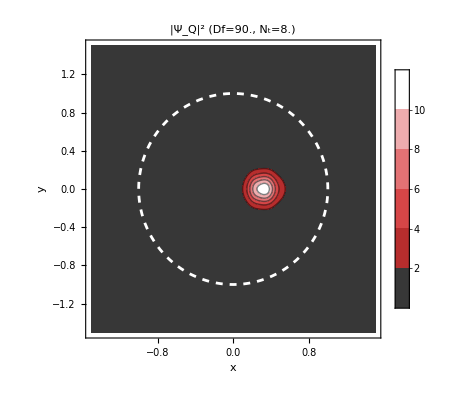
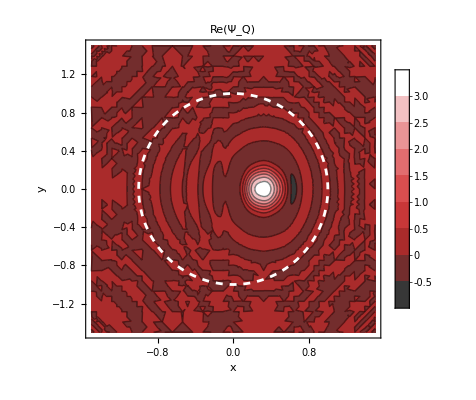
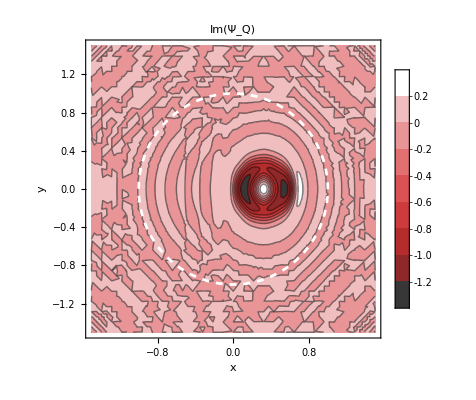
-Graphics- | -Graphics- | -Graphics-

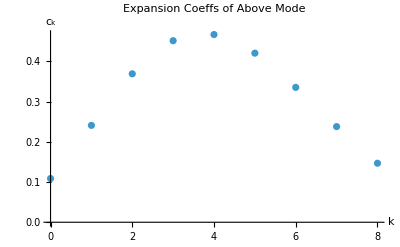

```mathematica
With[{Dfindex=1,Ntotindex=4,wenhuacvals=Values[#[[-1,-1]]]&/@#&/@wenhuasols},With[{MS=Length[wenhuacvals[[1,1]]]-1},
optθs=Table[n π/4,{n,0,MS}];
wenhuamodes=(# Exp[1.I optθs]).Table[HGmodeTransmit[n,0],{n,0,MS}]&/@#&/@wenhuacvals;
CompileFunctions[MS,defineWenhuaFunction-> True];
Print["# of c vals: ",wenhuacvals[[1,1]]//Length];
Print["Σ_k|c_k|^2: ",Norm@wenhuacvals[[Dfindex,Ntotindex]]];
qcesatwenhuacvals=Series[- Log[1+d^2(Objectivefreducedcs@@#)],{d,0,2}]&(*Objectivefreducedcs@@#&*)/@#&/@Table[Join[Normalize@wenhuacvals[[i,j]],{0,0}(*optimal ϕrqpvector for wenhuas qfi for qprobe*),{wenhuaDfs[[i]],wenhuaNtots[[j]]}],{i,Length[wenhuaDfs]},{j,Length[wenhuaNtots]}];
PlotMode[wenhuamodes[[1,4]]/.{rT-> 1,rR-> 1,Df->wenhuaDfs[[1]]},PlotLabel-> {"|Ψ_Q|^2 (Df="<>ToString[wenhuaDfs[[Dfindex]]]<>", N_t="<>ToString[wenhuaNtots[[Ntotindex]]]<>")","Re(Ψ_Q)","Im(Ψ_Q)"}]//Print;
ListPlot[{Range[MS+1]-1,wenhuacvals[[Dfindex,Ntotindex]]}ᵀ,PlotLabel-> "Expansion Coeffs of Above Mode",
AxesLabel->(Style[#,FontFamily->"Times",FontSize->14]&/@{"k","c_k"})]]//Print];
```

```mathematica
cs
```

{Cos[ϕc0],Cos[ϕc1] Sin[ϕc0],Cos[ϕc2] Sin[ϕc0] Sin[ϕc1],Cos[ϕc3] Sin[ϕc0] Sin[ϕc1] Sin[ϕc2],Cos[ϕc4] Sin[ϕc0] Sin[ϕc1] Sin[ϕc2] Sin[ϕc3],Cos[ϕc5] Sin[ϕc0] Sin[ϕc1] Sin[ϕc2] Sin[ϕc3] Sin[ϕc4],Cos[ϕc6] Sin[ϕc0] Sin[ϕc1] Sin[ϕc2] Sin[ϕc3] Sin[ϕc4] Sin[ϕc5],Cos[ϕc7] Sin[ϕc0] Sin[ϕc1] Sin[ϕc2] Sin[ϕc3] Sin[ϕc4] Sin[ϕc5] Sin[ϕc6],Sin[ϕc0] Sin[ϕc1] Sin[ϕc2] Sin[ϕc3] Sin[ϕc4] Sin[ϕc5] Sin[ϕc6] Sin[ϕc7]}

```mathematica
qcesatwenhuacvals//MatrixForm
```

(5054.21 d^2+O[d]^3 | -9368.01 d^2+O[d]^3 | -16987. d^2+O[d]^3 | -23562.1 d^2+O[d]^3 | -32482.1 d^2+O[d]^3 | -74837. d^2+O[d]^3 | -236976. d^2+O[d]^3
10247.7 d^2+O[d]^3 | -6916.27 d^2+O[d]^3 | -15969.8 d^2+O[d]^3 | -24137.1 d^2+O[d]^3 | -34521.8 d^2+O[d]^3 | -81051.3 d^2+O[d]^3 | -256834. d^2+O[d]^3
91797.4 d^2+O[d]^3 | 54757.5 d^2+O[d]^3 | 24299.6 d^2+O[d]^3 | -6191.21 d^2+O[d]^3 | -35417.9 d^2+O[d]^3 | -120904. d^2+O[d]^3 | -400617. d^2+O[d]^3
448633. d^2+O[d]^3 | 367874. d^2+O[d]^3 | 263789. d^2+O[d]^3 | 153977. d^2+O[d]^3 | 55769.6 d^2+O[d]^3 | -127651. d^2+O[d]^3 | -541776. d^2+O[d]^3)

↓Spatial profile and Gaussian state optimization of probe excited in single-mode state under a mean photon number constraint

```mathematica
(*If running on HPC, Run this block by calling LaunchKernels[n] where n is the number of requested cores*)
```

```mathematica
ClearParams[];
LaunchKernels[];
```

```mathematica
Kernels[]
```

{}

```mathematica
CloseKernels[];
```

```mathematica
<<CCompilerDriver`
```

```mathematica
(*Check C-compilers automatically detected by mathematica*)
CCompilers[Full]
```

{{Name→Intel Compiler,Compiler→CCompilerDriver`IntelCompiler`IntelCompiler,CompilerInstallation→None,CompilerName→Automatic},{Name→Generic C Compiler,Compiler→CCompilerDriver`GenericCCompiler`GenericCCompiler,CompilerInstallation→None,CompilerName→Automatic}}

```mathematica
(*$CCompiler=CCompilers[][[1]]*)(*Run this command if MSVC build tools are installed and detected by CCompilers[]*)
```

```mathematica
(*Set this with appropriate paths if using mingw64 compiler*)
$CCompiler={"Compiler"->CCompilerDriver`GenericCCompiler`GenericCCompiler,"CompilerInstallation"->"C:\\ProgramData\\mingw64\\mingw64\\bin",
"CompilerName"->"gcc.exe"
(*---Uncomment below line to explicitly specify Mathematica's compiler directories - this is usually handled automatically.---*)
,"Libraries"->{"WolframRTL"},"LibraryDirectories"->{"C:\\Program Files\\Wolfram Research\\Mathematica\\12.1\\SystemFiles\\Libraries\\Windows-x86-64"},
(*↓First 3 parameters are for optimization of math expression in C-compiled code*)"CompileOptions"->{"-O3","-march=native","-ffast-math","-static-libgcc"(*for robustness against mathematica crashes*)}
(*---Uncomment the below two lines for debugging the C-Compilation---*)
,"ShellCommandFunction"-> Print,(*Prints the command given to shell to compile the funciton*)
"ShellOutputFunction"-> Print(*Prints the output fromt the shell-compilation command*)};
(*Clear[$CCompiler]*)
```

```mathematica
<<CompiledFunctionTools`(*Tools for debugging Compile-related code*)
<<Compiler`(*More Tools for debugging FunctionCompile-related code—not available in version 12.1*)
```

Get::noopen: Cannot open Compiler`.

$Failed

```mathematica
(*in12.1, use FunctionCompileExportString with option LLVM or Assembly when defining a compiled function cf to get internal workings. Another tool is InputForm[cf],to see the basic properties of the compiledfunction.*)
```

```mathematica
(*Clear only cs definition*)
ClearParams[onlycs-> True]
```

```mathematica
(*redefine cs in terms of polar coordinates*)
ToString[cs]<>"=Product[Sin[ϕcs[[i]]],{i,1,#}]Cos[ϕcs[[#+1]]]&/@Range[0,"<>ToString[MSold]<>"]"//ToExpression;
```

```mathematica
funcargscs
```

{Cos[ϕc0],Cos[ϕc1] Sin[ϕc0],Sin[ϕc0] Sin[ϕc1],ϕrqp0,ϕrqp1,Df,Ntot}

```mathematica
sol2
```

{0.683012701892219,{ϕc0→0.477658286089882,ϕc1→1.57079628596802}}

```mathematica
funcargsreduced
```

{ϕc0,ϕc1,ϕrqp0,ϕrqp1,Df,Ntot}

```mathematica
funcargscs
```

{Cos[ϕc0],Cos[ϕc1] Sin[ϕc0],Sin[ϕc0] Sin[ϕc1],ϕrqp0,ϕrqp1,Df,Ntot}

```mathematica
AbsoluteTiming[qssimpcoeffd2reducedcsComp@@(funcargscs/.Join[sol2[[2]],{ϕrqp0-> π/2.,ϕrqp1-> 0.,Df-> 300.,Ntot-> 16.}])]
```

CompiledCodeFunction::argtype: Argument type at position 1 does not match function signature.

{0.0015869,Failure[…]}

```mathematica
AbsoluteTiming[qssimpcoeffd2reducedComp@@(funcargsreduced/.Join[sol1[[2]],{Df-> 300,Ntot-> 16}])]
```

{0.0001297,-26195.5}

ηfres: 0.861626

Calculated MSin: 10

rqp unit vec: {Cos[ϕrqp0],Cos[ϕrqp1] Sin[ϕrqp0],Sin[ϕrqp0] Sin[ϕrqp1]}

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

optimal quantum probe cs: {0.27748903788367,0.39556592741699,0.48233078868506,0.46709013635047,0.40105593242711,0.30179559065819,0.20622290283597,0.12487106655885,0.070085527063364,0.024885709805125,0.011526390678616} (Total: 1.)

Transmissivity of optimal mode with squeezing allowed: 0.586408

Transmissivity of optimal mode for coherent probe: 0.370079

Phase gate phase: 15.9896d

Reflectivity of leakage mode BS: 6.78885 d^2

optimal quantum probe rqps: {2.09471,1.83853×10^-8,8.22112×10^-8}

N1 (displacement mean-photon allocation): 1.77417×10^-15

N2 (squeezing mean-photon allocation): 16.

Quantum Probe Chernoff Exponent: 3327.13780409956 d^2+O[d]^3

Optimal Quantum Probe:

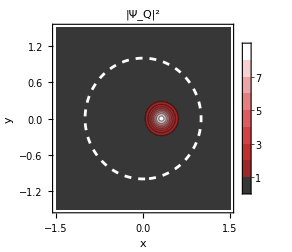
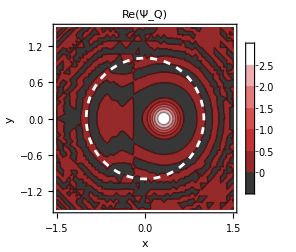
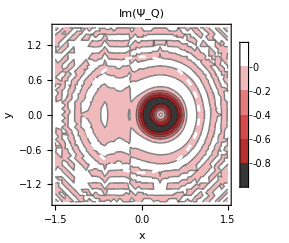
-Graphics- | -Graphics- | -Graphics-

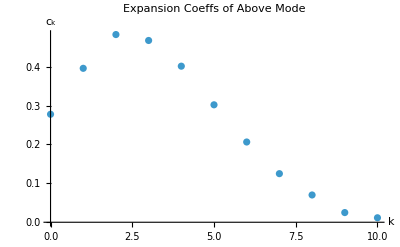

Classical Probe Chernoff Exponent: 3439.45 d^2

Optimal Classical Mode:

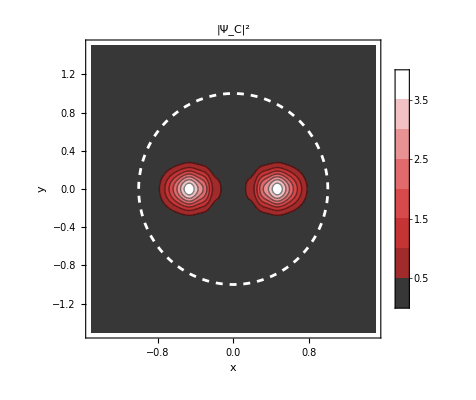
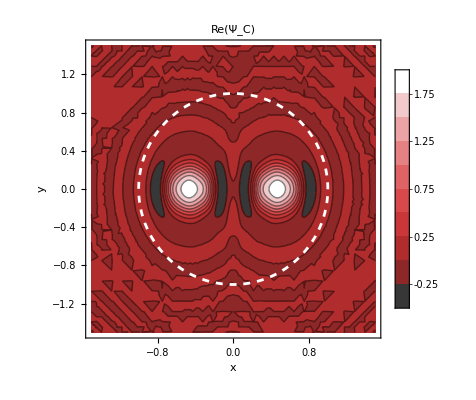
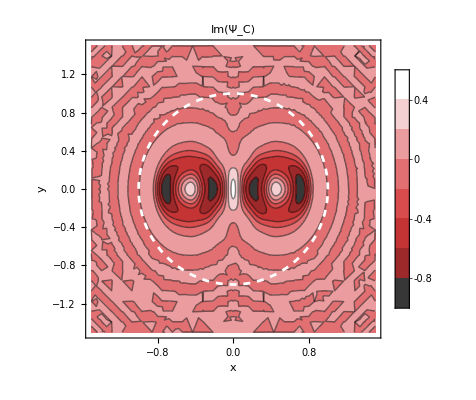
-Graphics- | -Graphics- | -Graphics-

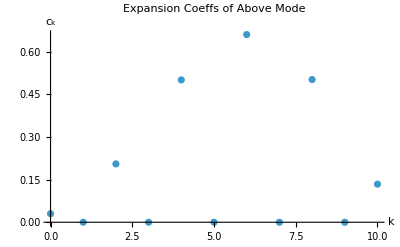

```mathematica
With[{Ntotin=16.,Dfin=45.,cutoffthresh=10^(-.6)},
With[{ηfresin=GetLoss[Dfin]},
Print["ηfres: ",ηfresin];
With[{MSin=Log[ηfresin,cutoffthresh ηfresin]-1//Ceiling},
Print["Calculated MSin: ",MSin];
CompileFunctions[MSin,compilationTarget-> "WVM"];
sols1=SortBy[ParallelTable[
AbsoluteTiming@Optimalcoeffd2reduced[Ntotin,Dfin,AllowSqueezing-> True,(*DifferetialEvolution doesn't seem to do better for 1000 search points here*)
Method-> (*{"DifferentialEvolution","SearchPoints"-> 500,"RandomSeed"-> rs,"ScalingFactor"-> .8}*)(*{"RandomSearch","SearchPoints"->Automatic,"RandomSeed"-> rs}*){"NelderMead","ShrinkRatio"-> .85,"ContractRatio"-> .85,"ReflectRatio"-> 2,"RandomSeed"->rs}],
{rs,1, Max[2 Length[Kernels[]],1]}],#[[2,1]]&(*Each element of sols1 has the format {runtime(ms),{sol,{parameter assignment rules for sol}}}; want to sort by sol*)];
sol1=sols1[[1,2]];(*select the first element of the solution list, neglecting timing*)
sol2=OptimalQCEby4NrootDfdsqclassical[Dfin];(*Hand-derived classical probe QCE*);
Clear[transmitmode];
{transmitmode,transmitmode2}=(cs Exp[1.I #]).Table[HGmodeTransmit[n,0],{n,0,MSin}]&/@{optθs,optθs2};
(*Print["Qprobe solution: ",sol1];*)
Print["optimal quantum probe cs: ", #," (Total: ",#^2//Total,")"]&@(cs/.sol1[[2]]);
Print["Transmissivity of optimal mode with squeezing allowed: ",η/.sol1[[2]]/.Df-> Dfin];
Print["Transmissivity of optimal mode for coherent probe: ",η/.sol2[[2]]/.Df-> Dfin];
Print["Phase gate phase: ",ϵ0reduced/.sol1[[2]]/.Df-> Dfin,d];
Print["Reflectivity of leakage mode BS: ",ϵ1sqreduced/.sol1[[2]]/.Df-> Dfin//Sqrt ,d^2];
Print["optimal quantum probe rqps: ",{r,q1,p1}/.sol1[[2]]/.Ntot-> Ntotin];
Print["N1 (displacement mean-photon allocation): ",(q1^2+p1^2)/4/.sol1[[2]]/.Ntot-> Ntotin];
Print["N2 (squeezing mean-photon allocation): ",Sinh[r]^2/.sol1[[2]]/.Ntot-> Ntotin//N[#,5]&];
(*Print["ϵ_0 coefficient: ",ϵ0coeffshalfComp@@(Join[ϕcs[[;;-2]],ϕrqps[[;;-2]],{Dfin,Ntotin}]/.sol1[[2]])];
Print["ϵ coefficient: ",ϵcoeffshalfComp@@(Join[ϕcs[[;;-2]],ϕrqps[[;;-2]],{Dfin,Ntotin}]/.sol1[[2]])];*)
Print["Quantum Probe Chernoff Exponent: ",Series[-Log[1+sol1[[1]] d^2],{d,0,2}]];
(*Clear[qprobeOptTransmitMode];*)
(*qprobeOptTransmitMode=Compile[{{x,_Real},{y,_Real}},transmitmode/.sol1[[2]]/.{rT-> 1,rR-> 1,Df-> Dfin}//Evaluate,CompilationOptions->{"InlineExternalDefinitions" -> True,"ExpressionOptimization" -> True}];*)
(*qprobeOptTransmitMode[x,y];*)
Print["Optimal Quantum Probe: "];
PlotMode[transmitmode/.sol1[[2]]/.{rT-> 1,rR-> 1,Df-> Dfin},PlotLabel-> {"|Ψ_Q|^2","Re(Ψ_Q)","Im(Ψ_Q)"}]//Print;
ListPlot[{Range[MSin+1]-1,cs/.sol1[[-1]]}ᵀ,PlotLabel-> "Expansion Coeffs of Above Mode",
AxesLabel->(Style[#,FontFamily->"Times",FontSize->20]&/@{"k","c_k"})]//Print;
Print["Classical Probe Chernoff Exponent: ",4√Dfin Ntotin sol2[[1]] d^2];
Print["Optimal Classical Mode:"];
PlotMode[(transmitmode/.sol2[[2]]/.{rT-> 1,rR-> 1,Df-> Dfin}),PlotLabel-> {"|Ψ_C|^2","Re(Ψ_C)","Im(Ψ_C)"}]//Print;
ListPlot[{Range[MSin+1]-1,cs/.sol2[[-1]]}ᵀ,PlotLabel-> "Expansion Coeffs of Above Mode",
AxesLabel->(Style[#,FontFamily->"Times",FontSize->16]&/@{"k","c_k"})]//Print
(*;Print["Optimal Classical Mode (π/2-shifted even phases): "];
PlotMode[transmitmode2/.sol2[[2]]/.{rT-> 1,rR-> 1,Df-> Dfin}, PlotLabel-> {"|Ψ_C|^2 (θ_(2 k)-> θ_(2 k)+π/2)","Re(Ψ_C)","Im(Ψ_C)"}]//Print;
*)
(*------↑Commented code: Plot of Mistaken "alternative" probe mode. In reality, a state exciting this mode will have a different QCB------*)
(*------↓Commented code: Plot of -ln(Qs) as a function of s at optimized parameters-----*)
(*
Plot[-Objectivef@@(funcargs/.Join[sol1[[2,;;-2]],{Df-> Dfin,Ntot-> Ntotin}]),{s,.01,.99},
AxesLabel->(Style[#,FontSize->16]&/@{"s","ξ/d^2"}),
PlotLabel->Style["-Log[Tr(ρ_0^s ρ_d^(1 - s))] of \n optimized probe (D_f="<>ToString[Dfin]<>",N="<>ToString[Ntotin]<>",M_S="<>ToString[MSin]<>")",FontSize->14]];*)
]]]
```

```mathematica
(*Numerical Conversion examination (possible massaging for Function Compile)*)
qssimpcoeffd2shalfred//N[#]&
```

(16. √Df (0.353553 ((1.+2. Df-1. √(1.+4. Df))/Df)^(3/2) Cos[ϕc0] Cos[ϕc1] Sin[ϕc0]+0.25 ((1.+2. Df-1. √(1.+4. Df))/Df)^(5/2) Cos[ϕc1] Sin[ϕc0]^2 Sin[ϕc1])^2 (-0.25+ϵ1^2+(-1.+2.71828^(-2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)+(-1.+2.71828^(2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)+(0.0625 ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)^2)/(√Df (0.353553 ((1.+2. Df-1. √(1.+4. Df))/Df)^(3/2) Cos[ϕc0] Cos[ϕc1] Sin[ϕc0]+0.25 ((1.+2. Df-1. √(1.+4. Df))/Df)^(5/2) Cos[ϕc1] Sin[ϕc0]^2 Sin[ϕc1])^2)+((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3) (4. Ntot Cos[ϕrqp1]^2 Sin[ϕrqp0]^2+4. Ntot Sin[ϕrqp0]^2 Sin[ϕrqp1]^2)))/((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)^2-(2. √Df (0.353553 ((1.+2. Df-1. √(1.+4. Df))/Df)^(3/2) Cos[ϕc0] Cos[ϕc1] Sin[ϕc0]+0.25 ((1.+2. Df-1. √(1.+4. Df))/Df)^(5/2) Cos[ϕc1] Sin[ϕc0]^2 Sin[ϕc1])^2 (((-1.+2.71828^(-2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)-1. (-1.+2.71828^(2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3))^2-8. Ntot Cos[ϕrqp1]^2 √Max[0.,-1.+(1.+(-1.+2.71828^(-2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)) (1.+(-1.+2.71828^(2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3))] ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3) (1.+(-1.+2.71828^(-2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3))^(3/2) √(1.+(-1.+2.71828^(2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)) Sin[ϕrqp0]^2-8. Ntot √Max[0.,-1.+(1.+(-1.+2.71828^(-2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)) (1.+(-1.+2.71828^(2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3))] ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3) √(1.+(-1.+2.71828^(-2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)) (1.+(-1.+2.71828^(2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3))^(3/2) Sin[ϕrqp0]^2 Sin[ϕrqp1]^2+2. ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3) (1.+(-1.+2.71828^(-2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)) (1.+(-1.+2.71828^(2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)) (4. Ntot Cos[ϕrqp1]^2 (1.+(-1.+2.71828^(-2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)) Sin[ϕrqp0]^2+4. Ntot (1.+(-1.+2.71828^(2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)) Sin[ϕrqp0]^2 Sin[ϕrqp1]^2)))/(((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)^2 (1.+(-1.+2.71828^(-2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)) (1.+(-1.+2.71828^(2. ArcSinh[√Ntot Cos[ϕrqp0]])) ((0.5 (1.+2. Df-1. √(1.+4. Df)) Cos[ϕc0]^2)/Df+(0.25 (1.+2. Df-1. √(1.+4. Df))^2 Cos[ϕc1]^2 Sin[ϕc0]^2)/Df^2+(0.125 (1.+2. Df-1. √(1.+4. Df))^3 Sin[ϕc0]^2 Sin[ϕc1]^2)/Df^3)))

```mathematica
sols1//First
```

{5.19116,{-44479.6045650076,{ϕc0→1.57079630224806,ϕc1→1.57076505572296,ϕc2→1.57079629584562,ϕc3→1.57049064584808,ϕc4→1.57079628292057,ϕc5→1.56897686949287,ϕc6→1.57079624510139,ϕc7→1.56315862374436,ϕc8→1.57079613601566,ϕc9→1.54643606016226,ϕc10→1.57079588819723,ϕc11→1.50899299542751,ϕc12→1.5707954270433,ϕc13→1.44191294564026,ϕc14→1.57079470871939,ϕc15→1.34349559167444,ϕc16→1.57079376271592,ϕc17→1.22168818307718,ϕc18→1.57079269763818,ϕc19→1.08915032155397,ϕc20→1.57079161596067,ϕc21→0.955702117796134,ϕc22→1.57079054949623,ϕc23→0.823926378074435,ϕc24→1.57078953949338,ϕc25→0.686983075413119,ϕc26→1.57078858863303,ϕc27→0.521457647692373,ϕc28→1.57078766784843,ϕc29→0.239463595144366,ϕc30→1.57078767536361,ϕrqp0→1.5708,ϕrqp1→6.18789692298853}}}

```mathematica
(*Observations: 
1. At low total photon number, the squeezing-prohibited optimization of the compiled qsreduced function qssimpcoeffd2reducedComp has a harder time finding the global optimum.<--Due to its erroneous outputs with small imaginary parts that throw off NMinimize, which fails to compare values at erroneous points of the search space.
2. When plugged in the optimum parameters for the hand-derived qscomp function, qssimpcoeffd2reducedComp returns the optimal qce that agrees with the hand-derived function.
3. The Optimalcoeffd2 functions can be run by directly optimizing the expression Re@qssimpcoeffd2shalfred/.ϵ1^2->ϵ1sqreduced without any runtime errors, but the compiled version is much faster (14s vs 57s at (Ntot,Df)=(16,500)).
4. At very low Df there seems to be no benefit offered by squeezing.
5. Compilation to C MinGW-x64 doesn't reduce the run time of this code (likely due to large math expression -- runs about 30% slower than WVM).
6. FunctionCompile takes a heck of a long time to compile. Might outweigh benefits if large amounts of Df samples are to be evaluated.*)
```

```mathematica
<<CompiledFunctionTools`
```

```mathematica
(*Compiled instructions with real arguments*)
CompilePrint[qssimpcoeffd2reducedComp]
```

14 arguments
		15 Integer registers
		190 Real registers
		Underflow checking off
		Overflow checking on
		Integer overflow checking on
		RuntimeAttributes -> {}

		R0 = A1
		R1 = A2
		R2 = A3
		R3 = A4
		R4 = A5
		R5 = A6
		R6 = A7
		R7 = A8
		R8 = A9
		R9 = A10
		R10 = A11
		R11 = A12
		R12 = A13
		R13 = A14
		R113 = 2.5
		I6 = 7
		I8 = 9
		R136 = 7.5
		R54 = 0.5
		I7 = 8
		R176 = 0.1875
		R94 = 0.001953125
		R139 = 8.5
		R189 = 0.
		I11 = -2
		I12 = -1
		R112 = 3.5
		R169 = -0.25
		I14 = 16
		R133 = 6.5
		R64 = 0.125
		I13 = -16
		R181 = 0.046875
		I0 = 2
		R104 = 0.00048828125
		R186 = 27.5
		R107 = 1.5
		R180 = 0.078125
		I2 = 1
		R84 = 0.0078125
		R142 = 9.5
		R74 = 0.03125
		I5 = 6
		I3 = 3
		R127 = 4.5
		R99 = 0.0009765625
		I10 = 11
		R69 = 0.0625
		R89 = 0.00390625
		R184 = 0.02734375
		I9 = 10
		R79 = 0.015625
		R182 = 0.0234375
		R130 = 5.5
		R59 = 0.25
		R146 = 10.5
		I1 = 4
		I4 = 5
		R144 = 0.005859375
		Result = R171

1	R14 = Reciprocal[ R12]
2	R15 = I0
3	R15 = R15 * R12
4	R16 = I1
5	R16 = R16 * R12
6	R17 = I2
7	R17 = R17 + R16
8	R18 = Sqrt[ R17]
9	R19 = - R18
10	R20 = I2
11	R20 = R20 + R15 + R19
12	R21 = R14 * R20
13	R22 = Cos[ R1]
14	R23 = Sin[ R0]
15	R24 = Cos[ R2]
16	R25 = Square[ R23]
17	R26 = Sin[ R1]
18	R27 = I0
19	R28 = Internal`ReciprocalSqrt[ R27]
20	R27 = Cos[ R3]
21	R29 = Square[ R26]
22	R30 = Sin[ R2]
23	R31 = Cos[ R4]
24	R32 = Square[ R30]
25	R33 = Sin[ R3]
26	R34 = Cos[ R5]
27	R35 = Square[ R33]
28	R36 = Sin[ R4]
29	R37 = Cos[ R6]
30	R38 = Square[ R36]
31	R39 = Sin[ R5]
32	R40 = Cos[ R7]
33	R41 = Square[ R39]
34	R42 = Sin[ R6]
35	R43 = Cos[ R8]
36	R44 = Square[ R42]
37	R45 = Sin[ R7]
38	R46 = Cos[ R9]
39	R47 = Square[ R45]
40	R48 = Sin[ R8]
41	R49 = Cos[ R0]
42	R50 = Square[ R48]
43	R51 = Sin[ R9]
44	R52 = Sqrt[ R12]
45	R53 = Square[ R49]
46	R55 = R54 * R14 * R20 * R53
47	R56 = Square[ R12]
48	R57 = Reciprocal[ R56]
49	R56 = Square[ R20]
50	R58 = Square[ R22]
51	R60 = R59 * R57 * R56 * R58 * R25
52	R61 = Power[ R12, I3]
53	R62 = Reciprocal[ R61]
54	R61 = Power[ R20, I3]
55	R63 = Square[ R24]
56	R65 = R64 * R62 * R61 * R63 * R25 * R29
57	R66 = Power[ R12, I1]
58	R67 = Reciprocal[ R66]
59	R66 = Power[ R20, I1]
60	R68 = Square[ R27]
61	R70 = R69 * R67 * R66 * R68 * R25 * R29 * R32
62	R71 = Power[ R12, I4]
63	R72 = Reciprocal[ R71]
64	R71 = Power[ R20, I4]
65	R73 = Square[ R31]
66	R75 = R74 * R72 * R71 * R73 * R25 * R29 * R32 * R35
67	R76 = Power[ R12, I5]
68	R77 = Reciprocal[ R76]
69	R76 = Power[ R20, I5]
70	R78 = Square[ R34]
71	R80 = R79 * R77 * R76 * R78 * R25 * R29 * R32 * R35 * R38
72	R81 = Power[ R12, I6]
73	R82 = Reciprocal[ R81]
74	R81 = Power[ R20, I6]
75	R83 = Square[ R37]
76	R85 = R84 * R82 * R81 * R83 * R25 * R29 * R32 * R35 * R38 * R41
77	R86 = Power[ R12, I7]
78	R87 = Reciprocal[ R86]
79	R86 = Power[ R20, I7]
80	R88 = Square[ R40]
81	R90 = R89 * R87 * R86 * R88 * R25 * R29 * R32 * R35 * R38 * R41 * R44
82	R91 = Power[ R12, I8]
83	R92 = Reciprocal[ R91]
84	R91 = Power[ R20, I8]
85	R93 = Square[ R43]
86	R95 = R94 * R92 * R91 * R93 * R25 * R29 * R32 * R35 * R38 * R41 * R44 * R47
87	R96 = Power[ R12, I9]
88	R97 = Reciprocal[ R96]
89	R96 = Power[ R20, I9]
90	R98 = Square[ R46]
91	R100 = R99 * R97 * R96 * R98 * R25 * R29 * R32 * R35 * R38 * R41 * R44 * R47 * R50
92	R101 = Power[ R12, I10]
93	R102 = Reciprocal[ R101]
94	R101 = Power[ R20, I10]
95	R103 = Square[ R51]
96	R105 = R104 * R102 * R101 * R25 * R29 * R32 * R35 * R38 * R41 * R44 * R47 * R50 * R103
97	R106 = R55 + R60 + R65 + R70 + R75 + R80 + R85 + R90 + R95 + R100 + R105
98	R108 = Sqrt[ R107]
99	R109 = I3
100	R110 = Sqrt[ R109]
101	R109 = I4
102	R111 = Sqrt[ R109]
103	R109 = Sqrt[ R112]
104	R114 = Sqrt[ R113]
105	R115 = Sqrt[ R13]
106	R116 = Cos[ R10]
107	R117 = R115 * R116
108	R118 = ArcSinh[ R117]
109	R119 = Sin[ R10]
110	R120 = Square[ R119]
111	R121 = Power[ R21, R107]
112	R122 = R54 * R28 * R121 * R49 * R22 * R23
113	R123 = Power[ R21, R113]
114	R124 = R59 * R123 * R22 * R24 * R25 * R26
115	R125 = Power[ R21, R112]
116	R126 = R64 * R108 * R125 * R24 * R27 * R25 * R29 * R30
117	R128 = Power[ R21, R127]
118	R129 = R64 * R28 * R128 * R27 * R31 * R25 * R29 * R32 * R33
119	R131 = Power[ R21, R130]
120	R132 = R74 * R114 * R131 * R31 * R34 * R25 * R29 * R32 * R35 * R36
121	R134 = Power[ R21, R133]
122	R135 = R79 * R110 * R134 * R34 * R37 * R25 * R29 * R32 * R35 * R38 * R39
123	R137 = Power[ R21, R136]
124	R138 = R84 * R109 * R137 * R37 * R40 * R25 * R29 * R32 * R35 * R38 * R41 * R42
125	R140 = Power[ R21, R139]
126	R141 = R84 * R140 * R40 * R43 * R25 * R29 * R32 * R35 * R38 * R41 * R44 * R45
127	R143 = Power[ R21, R142]
128	R145 = R144 * R28 * R143 * R43 * R46 * R25 * R29 * R32 * R35 * R38 * R41 * R44 * R47 * R48
129	R147 = Power[ R21, R146]
130	R148 = R99 * R111 * R147 * R46 * R25 * R29 * R32 * R35 * R38 * R41 * R44 * R47 * R50 * R51
131	R149 = R122 + R124 + R126 + R129 + R132 + R135 + R138 + R141 + R145 + R148
132	R150 = Square[ R149]
133	R151 = Square[ R106]
134	R152 = Reciprocal[ R151]
135	R151 = I11
136	R151 = R151 * R118
137	R153 = Exp[ R151]
138	R154 = I12
139	R154 = R154 + R153
140	R155 = R154 * R106
141	R156 = I0
142	R156 = R156 * R118
143	R157 = Exp[ R156]
144	R158 = I12
145	R158 = R158 + R157
146	R159 = R158 * R106
147	R160 = I2
148	R160 = R160 + R155
149	R161 = I2
150	R161 = R161 + R159
151	R162 = Cos[ R11]
152	R163 = Square[ R162]
153	R164 = Sin[ R11]
154	R165 = Square[ R164]
155	R166 = I1
156	R166 = R166 * R13 * R163 * R160 * R120
157	R167 = I1
158	R167 = R167 * R13 * R161 * R120 * R165
159	R168 = R166 + R167
160	R170 = I13
161	R170 = R170 * R52 * R150 * R152
162	R171 = Reciprocal[ R106]
163	R172 = R59 * R108 * R62 * R61 * R49 * R24 * R23 * R26
164	R173 = R59 * R57 * R56 * R22 * R23
165	R174 = R64 * R110 * R67 * R66 * R27 * R23 * R26 * R30
166	R173 = R173 + R174
167	R174 = R22 * R23 * R173
168	R173 = R59 * R62 * R61 * R24 * R23 * R26
169	R175 = R69 * R111 * R72 * R71 * R31 * R23 * R26 * R30 * R33
170	R173 = R173 + R175
171	R175 = R24 * R23 * R26 * R173
172	R173 = R176 * R67 * R66 * R27 * R23 * R26 * R30
173	R177 = Sqrt[ R136]
174	R178 = R74 * R177 * R77 * R76 * R34 * R23 * R26 * R30 * R33 * R36
175	R173 = R173 + R178
176	R178 = R27 * R23 * R26 * R30 * R173
177	R173 = R64 * R72 * R71 * R31 * R23 * R26 * R30 * R33
178	R177 = Sqrt[ R146]
179	R179 = R79 * R177 * R82 * R81 * R37 * R23 * R26 * R30 * R33 * R36 * R39
180	R173 = R173 + R179
181	R179 = R31 * R23 * R26 * R30 * R33 * R173
182	R177 = R180 * R77 * R76 * R34 * R23 * R26 * R30 * R33 * R36
183	R173 = R79 * R109 * R87 * R86 * R40 * R23 * R26 * R30 * R33 * R36 * R39 * R42
184	R177 = R177 + R173
185	R173 = R34 * R23 * R26 * R30 * R33 * R36 * R177
186	R177 = R181 * R82 * R81 * R37 * R23 * R26 * R30 * R33 * R36 * R39
187	R183 = R182 * R28 * R92 * R91 * R43 * R23 * R26 * R30 * R33 * R36 * R39 * R42 * R45
188	R177 = R177 + R183
189	R183 = R37 * R23 * R26 * R30 * R33 * R36 * R39 * R177
190	R177 = R184 * R87 * R86 * R40 * R23 * R26 * R30 * R33 * R36 * R39 * R42
191	R185 = R144 * R114 * R97 * R96 * R46 * R23 * R26 * R30 * R33 * R36 * R39 * R42 * R45 * R48
192	R177 = R177 + R185
193	R185 = R40 * R23 * R26 * R30 * R33 * R36 * R39 * R42 * R177
194	R177 = R79 * R92 * R91 * R43 * R23 * R26 * R30 * R33 * R36 * R39 * R42 * R45
195	R187 = Sqrt[ R186]
196	R188 = R99 * R187 * R102 * R101 * R23 * R26 * R30 * R33 * R36 * R39 * R42 * R45 * R48 * R51
197	R177 = R177 + R188
198	R188 = R43 * R23 * R26 * R30 * R33 * R36 * R39 * R42 * R45 * R177
199	R172 = R172 + R174 + R175 + R178 + R179 + R173 + R183 + R185 + R188
200	R174 = I0
201	R174 = R174 * R171 * R172
202	R171 = I2
203	R171 = R171 + R174
204	R174 = I1
205	R174 = R174 * R52 * R171
206	R170 = R170 + R174
207	R174 = I1
208	R174 = R174 * R13 * R163 * R120
209	R171 = I1
210	R171 = R171 * R13 * R120 * R165
211	R174 = R174 + R171
212	R171 = R106 * R174
213	R174 = R155 + R159 + R171
214	R171 = R169 * R170 * R174
215	R174 = R160 * R161
216	R172 = I12
217	R172 = R172 + R174
218	R174 = MaxR[ R189, R172]]
219	R172 = Sqrt[ R174]
220	R174 = Internal`ReciprocalSqrt[ R160]
221	R175 = Internal`ReciprocalSqrt[ R161]
222	R178 = R59 * R172 * R106 * R174 * R175 * R168
223	R172 = Reciprocal[ R160]
224	R174 = Reciprocal[ R161]
225	R175 = Square[ R160]
226	R179 = Square[ R161]
227	R175 = R175 + R179
228	R172 = R172 * R174 * R175
229	R174 = - R172
230	R172 = I11
231	R172 = R172 * R106 * R168
232	R175 = I0
233	R175 = R175 + R174 + R172
234	R174 = R64 * R175
235	R178 = R178 + R174
236	R174 = I14
237	R174 = R174 * R52 * R150 * R152 * R178
238	R171 = R171 + R174
239	Return

```mathematica
(*Compiled instructions with complex arguments*)
CompilePrint[qssimpcoeffd2reducedComp]
```

14 arguments
		15 Integer registers
		36 Real registers
		158 Complex registers
		Underflow checking off
		Overflow checking off
		Integer overflow checking on
		RuntimeAttributes -> {}

		C0 = A1
		C1 = A2
		C2 = A3
		C3 = A4
		C4 = A5
		C5 = A6
		C6 = A7
		C7 = A8
		C8 = A9
		C9 = A10
		C10 = A11
		C11 = A12
		C12 = A13
		C13 = A14
		R25 = 9.5
		R32 = 0.046875
		R5 = 0.0625
		I13 = 128
		R11 = 0.0009765625
		I10 = 11
		R14 = 1.5
		R17 = 4.5
		R35 = 27.5
		R26 = 0.005859375
		R9 = 0.00390625
		R30 = 0.1875
		I8 = 9
		R34 = 0.02734375
		I9 = 10
		I1 = 4
		I7 = 8
		R12 = 0.00048828125
		R29 = 10.5
		I5 = 6
		R22 = 6.5
		I14 = -16
		R3 = 0.25
		I4 = 5
		I11 = -2
		R15 = 2.5
		R10 = 0.001953125
		I0 = 2
		R4 = 0.125
		I12 = -1
		R31 = 0.078125
		R19 = 5.5
		I6 = 7
		I2 = 1
		R24 = 8.5
		I3 = 3
		R8 = 0.0078125
		R2 = 0.5
		R23 = 7.5
		R16 = 3.5
		R1 = 0.
		R7 = 0.015625
		R6 = 0.03125
		R33 = 0.0234375
		Result = C147

1	R0 = I0
2	C14 = R0 + R1 I
3	C14 = C14 * C12
4	R0 = I1
5	C15 = R0 + R1 I
6	C15 = C15 * C12
7	R0 = I2
8	C16 = R0 + R1 I
9	C16 = C16 + C15
10	C17 = Sqrt[ C16]
11	C18 = - C17
12	R0 = I2
13	C19 = R0 + R1 I
14	C19 = C19 + C14 + C18
15	C20 = Sin[ C0]
16	C21 = Square[ C20]
17	C22 = Sin[ C1]
18	C23 = Square[ C22]
19	C24 = Sin[ C2]
20	C25 = Square[ C24]
21	C26 = Sin[ C3]
22	C27 = Square[ C26]
23	C28 = Sin[ C4]
24	C29 = Square[ C28]
25	C30 = Sin[ C5]
26	C31 = Square[ C30]
27	C32 = Sin[ C6]
28	C33 = Square[ C32]
29	C34 = Sin[ C7]
30	C35 = Square[ C34]
31	C36 = Sin[ C8]
32	C37 = Square[ C36]
33	C38 = Sqrt[ C13]
34	C39 = Cos[ C10]
35	C40 = C38 * C39
36	C41 = ArcSinh[ C40]
37	C42 = Reciprocal[ C12]
38	C43 = Cos[ C0]
39	C44 = Square[ C43]
40	C45 = R2 + R1 I
41	C45 = C45 * C42 * C19 * C44
42	C46 = Square[ C12]
43	C47 = Reciprocal[ C46]
44	C46 = Square[ C19]
45	C48 = Cos[ C1]
46	C49 = Square[ C48]
47	C50 = R3 + R1 I
48	C50 = C50 * C47 * C46 * C49 * C21
49	C51 = Power[ C12, I3]
50	C52 = Reciprocal[ C51]
51	C51 = Power[ C19, I3]
52	C53 = Cos[ C2]
53	C54 = Square[ C53]
54	C55 = R4 + R1 I
55	C55 = C55 * C52 * C51 * C54 * C21 * C23
56	C56 = Power[ C12, I1]
57	C57 = Reciprocal[ C56]
58	C56 = Power[ C19, I1]
59	C58 = Cos[ C3]
60	C59 = Square[ C58]
61	C60 = R5 + R1 I
62	C60 = C60 * C57 * C56 * C59 * C21 * C23 * C25
63	C61 = Power[ C12, I4]
64	C62 = Reciprocal[ C61]
65	C61 = Power[ C19, I4]
66	C63 = Cos[ C4]
67	C64 = Square[ C63]
68	C65 = R6 + R1 I
69	C65 = C65 * C62 * C61 * C64 * C21 * C23 * C25 * C27
70	C66 = Power[ C12, I5]
71	C67 = Reciprocal[ C66]
72	C66 = Power[ C19, I5]
73	C68 = Cos[ C5]
74	C69 = Square[ C68]
75	C70 = R7 + R1 I
76	C70 = C70 * C67 * C66 * C69 * C21 * C23 * C25 * C27 * C29
77	C71 = Power[ C12, I6]
78	C72 = Reciprocal[ C71]
79	C71 = Power[ C19, I6]
80	C73 = Cos[ C6]
81	C74 = Square[ C73]
82	C75 = R8 + R1 I
83	C75 = C75 * C72 * C71 * C74 * C21 * C23 * C25 * C27 * C29 * C31
84	C76 = Power[ C12, I7]
85	C77 = Reciprocal[ C76]
86	C76 = Power[ C19, I7]
87	C78 = Cos[ C7]
88	C79 = Square[ C78]
89	C80 = R9 + R1 I
90	C80 = C80 * C77 * C76 * C79 * C21 * C23 * C25 * C27 * C29 * C31 * C33
91	C81 = Power[ C12, I8]
92	C82 = Reciprocal[ C81]
93	C81 = Power[ C19, I8]
94	C83 = Cos[ C8]
95	C84 = Square[ C83]
96	C85 = R10 + R1 I
97	C85 = C85 * C82 * C81 * C84 * C21 * C23 * C25 * C27 * C29 * C31 * C33 * C35
98	C86 = Power[ C12, I9]
99	C87 = Reciprocal[ C86]
100	C86 = Power[ C19, I9]
101	C88 = Cos[ C9]
102	C89 = Square[ C88]
103	C90 = R11 + R1 I
104	C90 = C90 * C87 * C86 * C89 * C21 * C23 * C25 * C27 * C29 * C31 * C33 * C35 * C37
105	C91 = Power[ C12, I10]
106	C92 = Reciprocal[ C91]
107	C91 = Power[ C19, I10]
108	C93 = Sin[ C9]
109	C94 = Square[ C93]
110	C95 = R12 + R1 I
111	C95 = C95 * C92 * C91 * C21 * C23 * C25 * C27 * C29 * C31 * C33 * C35 * C37 * C94
112	C96 = C45 + C50 + C55 + C60 + C65 + C70 + C75 + C80 + C85 + C90 + C95
113	C97 = C42 * C19
114	R0 = I0
115	R13 = Internal`ReciprocalSqrt[ R0]
116	R0 = I11
117	C98 = R0 + R1 I
118	C98 = C98 * C41
119	C99 = Exp[ C98]
120	R0 = I12
121	C100 = R0 + R1 I
122	C100 = C100 + C99
123	C101 = C100 * C96
124	R0 = I2
125	C102 = R0 + R1 I
126	C102 = C102 + C101
127	R0 = I0
128	C103 = R0 + R1 I
129	C103 = C103 * C41
130	C104 = Exp[ C103]
131	R0 = I12
132	C105 = R0 + R1 I
133	C105 = C105 + C104
134	C106 = C105 * C96
135	R0 = I2
136	C107 = R0 + R1 I
137	C107 = C107 + C106
138	C108 = Sqrt[ C12]
139	C109 = Power[ C97, R14]
140	C110 = R2 + R1 I
141	C111 = R13 + R1 I
142	C110 = C110 * C111 * C109 * C43 * C48 * C20
143	C111 = Power[ C97, R15]
144	C112 = R3 + R1 I
145	C112 = C112 * C111 * C48 * C53 * C21 * C22
146	R0 = Sqrt[ R14]
147	C113 = Power[ C97, R16]
148	C114 = R4 + R1 I
149	C115 = R0 + R1 I
150	C114 = C114 * C115 * C113 * C53 * C58 * C21 * C23 * C24
151	C115 = Power[ C97, R17]
152	C116 = R4 + R1 I
153	C117 = R13 + R1 I
154	C116 = C116 * C117 * C115 * C58 * C63 * C21 * C23 * C25 * C26
155	R18 = Sqrt[ R15]
156	C117 = Power[ C97, R19]
157	C118 = R6 + R1 I
158	C119 = R18 + R1 I
159	C118 = C118 * C119 * C117 * C63 * C68 * C21 * C23 * C25 * C27 * C28
160	R20 = I3
161	R21 = Sqrt[ R20]
162	C119 = Power[ C97, R22]
163	C120 = R7 + R1 I
164	C121 = R21 + R1 I
165	C120 = C120 * C121 * C119 * C68 * C73 * C21 * C23 * C25 * C27 * C29 * C30
166	R20 = Sqrt[ R16]
167	C121 = Power[ C97, R23]
168	C122 = R8 + R1 I
169	C123 = R20 + R1 I
170	C122 = C122 * C123 * C121 * C73 * C78 * C21 * C23 * C25 * C27 * C29 * C31 * C32
171	C123 = Power[ C97, R24]
172	C124 = R8 + R1 I
173	C124 = C124 * C123 * C78 * C83 * C21 * C23 * C25 * C27 * C29 * C31 * C33 * C34
174	C125 = Power[ C97, R25]
175	C126 = R26 + R1 I
176	C127 = R13 + R1 I
177	C126 = C126 * C127 * C125 * C83 * C88 * C21 * C23 * C25 * C27 * C29 * C31 * C33 * C35 * C36
178	R27 = I4
179	R28 = Sqrt[ R27]
180	C127 = Power[ C97, R29]
181	C128 = R11 + R1 I
182	C129 = R28 + R1 I
183	C128 = C128 * C129 * C127 * C88 * C21 * C23 * C25 * C27 * C29 * C31 * C33 * C35 * C37 * C93
184	C129 = C110 + C112 + C114 + C116 + C118 + C120 + C122 + C124 + C126 + C128
185	C130 = Square[ C129]
186	C131 = Reciprocal[ C96]
187	C132 = C102 * C107
188	R27 = I12
189	C133 = R27 + R1 I
190	C133 = C133 + C132
191	C134 = Sqrt[ C133]
192	C135 = Sin[ C10]
193	C136 = Square[ C135]
194	C137 = Cos[ C11]
195	C138 = Square[ C137]
196	C139 = Sin[ C11]
197	C140 = Square[ C139]
198	C141 = Square[ C96]
199	C142 = Reciprocal[ C141]
200	C141 = Reciprocal[ C102]
201	C143 = Reciprocal[ C107]
202	C144 = Power[ C102, R14]
203	C145 = Sqrt[ C107]
204	R27 = I13
205	C146 = R27 + R1 I
206	C146 = C146 * C108 * C13 * C138 * C130 * C131 * C144 * C145 * C134 * C136
207	C144 = Sqrt[ C102]
208	C145 = Power[ C107, R14]
209	R27 = I13
210	C147 = R27 + R1 I
211	C147 = C147 * C108 * C13 * C130 * C131 * C144 * C145 * C134 * C136 * C140
212	R27 = I14
213	C144 = R27 + R1 I
214	C144 = C144 * C108 * C130 * C142
215	C145 = R3 + R1 I
216	C148 = R0 + R1 I
217	C145 = C145 * C148 * C52 * C51 * C43 * C53 * C20 * C22
218	C148 = R3 + R1 I
219	C148 = C148 * C47 * C46 * C48 * C20
220	C149 = R4 + R1 I
221	C150 = R21 + R1 I
222	C149 = C149 * C150 * C57 * C56 * C58 * C20 * C22 * C24
223	C148 = C148 + C149
224	C149 = C48 * C20 * C148
225	C148 = R3 + R1 I
226	C148 = C148 * C52 * C51 * C53 * C20 * C22
227	C150 = R5 + R1 I
228	C151 = R28 + R1 I
229	C150 = C150 * C151 * C62 * C61 * C63 * C20 * C22 * C24 * C26
230	C148 = C148 + C150
231	C150 = C53 * C20 * C22 * C148
232	C148 = R30 + R1 I
233	C148 = C148 * C57 * C56 * C58 * C20 * C22 * C24
234	R27 = Sqrt[ R23]
235	C151 = R6 + R1 I
236	C152 = R27 + R1 I
237	C151 = C151 * C152 * C67 * C66 * C68 * C20 * C22 * C24 * C26 * C28
238	C148 = C148 + C151
239	C151 = C58 * C20 * C22 * C24 * C148
240	C148 = R4 + R1 I
241	C148 = C148 * C62 * C61 * C63 * C20 * C22 * C24 * C26
242	R27 = Sqrt[ R29]
243	C152 = R7 + R1 I
244	C153 = R27 + R1 I
245	C152 = C152 * C153 * C72 * C71 * C73 * C20 * C22 * C24 * C26 * C28 * C30
246	C148 = C148 + C152
247	C152 = C63 * C20 * C22 * C24 * C26 * C148
248	C148 = R31 + R1 I
249	C148 = C148 * C67 * C66 * C68 * C20 * C22 * C24 * C26 * C28
250	C153 = R7 + R1 I
251	C154 = R20 + R1 I
252	C153 = C153 * C154 * C77 * C76 * C78 * C20 * C22 * C24 * C26 * C28 * C30 * C32
253	C148 = C148 + C153
254	C153 = C68 * C20 * C22 * C24 * C26 * C28 * C148
255	C148 = R32 + R1 I
256	C148 = C148 * C72 * C71 * C73 * C20 * C22 * C24 * C26 * C28 * C30
257	C154 = R33 + R1 I
258	C155 = R13 + R1 I
259	C154 = C154 * C155 * C82 * C81 * C83 * C20 * C22 * C24 * C26 * C28 * C30 * C32 * C34
260	C148 = C148 + C154
261	C154 = C73 * C20 * C22 * C24 * C26 * C28 * C30 * C148
262	C148 = R34 + R1 I
263	C148 = C148 * C77 * C76 * C78 * C20 * C22 * C24 * C26 * C28 * C30 * C32
264	C155 = R26 + R1 I
265	C156 = R18 + R1 I
266	C155 = C155 * C156 * C87 * C86 * C88 * C20 * C22 * C24 * C26 * C28 * C30 * C32 * C34 * C36
267	C148 = C148 + C155
268	C155 = C78 * C20 * C22 * C24 * C26 * C28 * C30 * C32 * C148
269	C148 = R7 + R1 I
270	C148 = C148 * C82 * C81 * C83 * C20 * C22 * C24 * C26 * C28 * C30 * C32 * C34
271	R27 = Sqrt[ R35]
272	C156 = R11 + R1 I
273	C157 = R27 + R1 I
274	C156 = C156 * C157 * C92 * C91 * C20 * C22 * C24 * C26 * C28 * C30 * C32 * C34 * C36 * C93
275	C148 = C148 + C156
276	C156 = C83 * C20 * C22 * C24 * C26 * C28 * C30 * C32 * C34 * C148
277	C145 = C145 + C149 + C150 + C151 + C152 + C153 + C154 + C155 + C156
278	R27 = I0
279	C149 = R27 + R1 I
280	C149 = C149 * C131 * C145
281	R27 = I2
282	C145 = R27 + R1 I
283	C145 = C145 + C149
284	R27 = I1
285	C149 = R27 + R1 I
286	C149 = C149 * C108 * C145
287	C144 = C144 + C149
288	R27 = I1
289	C149 = R27 + R1 I
290	C149 = C149 * C13 * C138 * C136
291	R27 = I1
292	C145 = R27 + R1 I
293	C145 = C145 * C13 * C136 * C140
294	C149 = C149 + C145
295	C145 = C96 * C149
296	C149 = C101 + C106 + C145
297	R27 = I11
298	C145 = R27 + R1 I
299	C145 = C145 * C102 * C107 * C144 * C149
300	C144 = C105 * C96
301	C149 = - C144
302	C144 = C101 + C149
303	C149 = Square[ C144]
304	R27 = I1
305	C144 = R27 + R1 I
306	C144 = C144 * C13 * C138 * C102 * C136
307	R27 = I1
308	C150 = R27 + R1 I
309	C150 = C150 * C13 * C107 * C136 * C140
310	C144 = C144 + C150
311	R27 = I0
312	C150 = R27 + R1 I
313	C150 = C150 * C96 * C102 * C107 * C144
314	C149 = C149 + C150
315	R27 = I14
316	C150 = R27 + R1 I
317	C150 = C150 * C108 * C130 * C142 * C149
318	C146 = C146 + C147 + C145 + C150
319	C147 = R4 + R1 I
320	C147 = C147 * C141 * C143 * C146
321	Return

```mathematica
sols1
```

{{-3685.69668453016,{ϕc0→1.55909456161926,ϕc1→1.57079624654082,ϕc2→1.49706379422493,ϕc3→1.57079608820908,ϕc4→1.33901817867056,ϕc5→1.57079582336774,ϕc6→1.09828797589151,ϕc7→1.57079551528506,ϕc8→0.835266652766988,ϕc9→1.57079523674284,ϕc10→0.575860805447976,ϕc11→1.57079503197427,ϕc12→0.244971679203577,ϕc13→1.57079515879734,ϕrqp0→1.5708,ϕrqp1→6.07121577919521}},{-3685.69668453013,{ϕc0→1.55909456349774,ϕc1→1.57079624184326,ϕc2→1.49706378866641,ϕc3→1.57079605661067,ϕc4→1.33901817541918,ϕc5→1.57079572639146,ϕc6→1.0982879734581,ϕc7→1.57079533367333,ϕc8→0.835266651670322,ϕc9→1.57079495398754,ϕc10→0.575860814777117,ϕc11→1.57079462662922,ϕc12→0.244971685059207,ϕc13→1.57079454942583,ϕrqp0→1.5708,ϕrqp1→5.13360557054576}},{-3685.69668453012,{ϕc0→1.5590945575652,ϕc1→1.57079623691174,ϕc2→1.49706379476142,ϕc3→1.57079603323836,ϕc4→1.33901817909943,ϕc5→1.57079568104306,ϕc6→1.09828796199268,ϕc7→1.57079526660509,ϕc8→0.835266636210124,ϕc9→1.5707948766151,ϕc10→0.57586078999983,ϕc11→1.57079454246402,ϕc12→0.244971667863596,ϕc13→1.57079445880983,ϕrqp0→1.5708,ϕrqp1→5.00436344370612×10^-7}},{-3685.69668453009,{ϕc0→1.5590945645723,ϕc1→1.57079625496746,ϕc2→1.49706380826212,ϕc3→1.57079603223359,ϕc4→1.33901821114974,ϕc5→1.57079564354139,ϕc6→1.09828802669176,ϕc7→1.57079513103743,ϕc8→0.835266714553908,ϕc9→1.57079459707298,ϕc10→0.575860831935936,ϕc11→1.57079413712044,ϕc12→0.244971726089839,ϕc13→1.57079341258485,ϕrqp0→1.5708,ϕrqp1→3.47646095501311}},{-3685.69668453007,{ϕc0→1.55909456273038,ϕc1→1.57079622129872,ϕc2→1.49706378820723,ϕc3→1.57079597967681,ϕc4→1.339018173157,ϕc5→1.5707955465999,ϕc6→1.09828796410221,ϕc7→1.57079503577064,ϕc8→0.835266645835482,ϕc9→1.57079453543531,ϕc10→0.575860808372808,ϕc11→1.57079410797561,ϕc12→0.244971660896306,ϕc13→1.57079406965979,ϕrqp0→1.5708,ϕrqp1→1.39343726938499}},{-3592.12925558956,{ϕc0→1.57064806171271,ϕc1→1.48853618780055,ϕc10→0.52456668214468,ϕc11→1.5707924786103,ϕc12→0.267998102511649,ϕc13→1.570793037001,ϕc2→1.45845414172405,ϕc3→1.41844500929923,ϕc4→1.23650552484182,ϕc5→1.5707933430655,ϕc6→1.04119878688971,ϕc7→1.43415029131245,ϕc8→0.772898238790454,ϕc9→1.5707947466577,ϕrqp0→1.5708,ϕrqp1→6.28265965645982}},{-3561.14639010253,{ϕc0→1.570706829443,ϕc1→1.57031993416807,ϕc10→0.314525937300157,ϕc11→1.29861132395064,ϕc12→0.0000786659049436135,ϕc13→5.79394636071953×10^-8,ϕc2→1.570391458068,ϕc3→1.56753786661583,ϕc4→1.33808579401992,ϕc5→1.5707882686084,ϕc6→1.0117046528461,ϕc7→1.5705339636152,ϕc8→0.727935674037463,ϕc9→1.18768883564238,ϕrqp0→1.5708,ϕrqp1→6.28318480291843}},{-3538.30905602044,{ϕc0→1.5707957644914,ϕc1→1.3780760689326,ϕc10→1.5707890965274,ϕc11→0.114997752383268,ϕc12→1.02425611706719,ϕc13→1.11380882469389,ϕc2→1.5707906468017,ϕc3→1.30305928084596,ϕc4→1.54298011633023,ϕc5→1.11386765816937,ϕc6→1.47056488800591,ϕc7→0.772448136246852,ϕc8→1.45213675583699,ϕc9→0.576588812381801,ϕrqp0→1.5708,ϕrqp1→5.7447121401097}}}

```mathematica
qssimpcoeffd2reducedComp@@(funcargsreduced/.sol2[[2]]~Join~Assign[Join[ϕrqps[[;;-2]],{Ntot,Df}],{π/4,0,2.,90}])
```

-920.664

```mathematica
sol2[[2]]
```

{ϕc0→1.56539917115595,ϕc1→1.57079626184844,ϕc2→1.51797201254953,ϕc3→1.57079617513761,ϕc4→1.375438276574,ϕc5→1.5707959797262,ϕc6→1.13774575521036,ϕc7→1.57079573602021,ϕc8→0.865690495832616,ϕc9→1.57079551200444,ϕc10→0.593379265251486,ϕc11→1.57079530207909,ϕc12→0.24961124145707,ϕc13→1.57079517802912}

↓Showing that re-allocation of photons between squeezing and displacement does not affect optimal coherent probe, but does affect the optimal quantum probe:

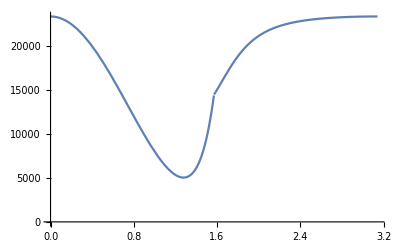

```mathematica
evaluatedqs=-qssimpcoeffd2shalfred/.ϵ1^2-> ϵ1sqreduced/.Join[Delete[sol1[[2]],-2],Assign[{Ntot,Df},{8,500}]];
(*squeezerQCEbydsqCompiled=Compile[{ϕrqp0},evaluatedqs,
CompilationOptions->{"ExpressionOptimization"-> True,"InlineExternalDefinitions"-> True},RuntimeOptions->"Speed"];
plotfunc[ϕrqp0_?NumericQ]:=squeezerQCEbydsqCompiled[ϕrqp0];*)(*↑What goes on under the hood of Plot when given a symbolic expression to plot*)
Plot[(*plotfunc[ϕrqp0]*)evaluatedqs,{ϕrqp0,0,π},PlotRange->{0,-sol1[[1]]}]
Clear[evaluatedqs];
```

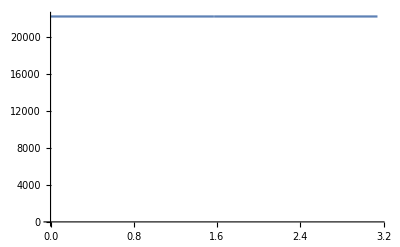

```mathematica
evaluatedqs=-qssimpcoeffd2shalfred/.ϵ1^2-> ϵ1sqreduced/.Join[sol2[[2]],Assign[{Ntot,Df,ϕrqp1},{8,500,0}]];
Plot[evaluatedqs,{ϕrqp0,0,π},PlotRange->{0,4 8 √500 sol2[[1]]+10}]
Clear[evaluatedqs];
```